```mathematica
SetDirectory[NotebookDirectory[]]
FS=26;(*Default font size*)
```

/home/vixer/articles/Dissertation/pics

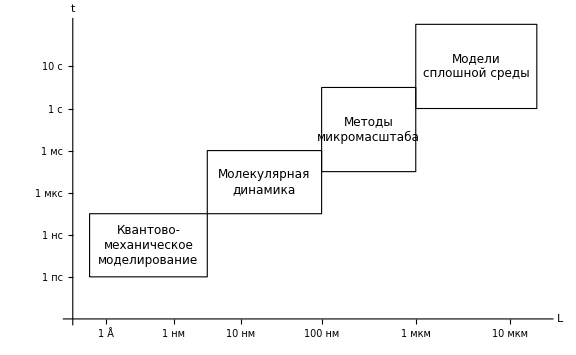

```mathematica
a1=Rectangle[{0.25,1},{2,2.5}];
a2=Rectangle[{2,2.5},{3.7,4}];
a3=Rectangle[{3.7,3.5},{5.1,5.5}];
a4=Rectangle[{5.1,5},{6.9,7}];
(*Export["ModelsHierarchy.pdf",*)
Show[
Plot[-1,{x,0,7},PlotRange->{{0,7},{0,7}},LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"L","t"},
Ticks->{
{{0.5,"1 Å"},{1.5,"1 нм"},{2.5,"10 нм"},{3.7,"100 нм"},{5.1,"1 мкм"},{6.5,"10 мкм"}},
{{1,"1 пс"},{2,"1 нс"},{3,"1 мкс"},{4,"1 мс"},{5,"1 с"},{6,"10 с"}}
}],
Graphics[{
FaceForm[White],EdgeForm[Directive[Thick,Black]],
a1,a2,a3,a4,
Text[Style["Квантово-\nмеханическое\nмоделирование",12],RegionCentroid[a1]],
Text[Style["Молекулярная\nдинамика",12],RegionCentroid[a2]],
Text[Style["Методы\nмикромасштаба",12],RegionCentroid[a3]],
Text[Style["Модели\nсплошной среды",12],RegionCentroid[a4]],
}],
ImageSize->Large
]
```

# Функции нелокального влияния

```mathematica
ρ[x1_,x2_,r1_,r2_,n_]:=(Abs[x1/r1]^n+Abs[x2/r2]^n)^(1/n);
φP[x1_,x2_,r1_,r2_,n_,p_,q_]:=Piecewise[{{(n p(1-ρ[x1,x2,r1,r2,n]^p)^q)/(4 r1 r2 Beta[1/n,1/n]Beta[2/p,q+1]), ρ[x1,x2,r1,r2,n]<=1}, {0, True}}];
φE[x1_,x2_,r1_,r2_,n_,p_,q_]:=(4^(1/n)n p q^(2/p)Exp[-q ρ[x1,x2,r1,r2,n]^p])/(8r1 r2  Beta[1/n,1/2]Gamma[2/p]);
```

```mathematica
φP[x1,x2,r,r,2,2,1]
```

Piecewise[{{(2 (1-Abs[x1/r]^2-Abs[x2/r]^2))/(π r^2), √(Abs[x1/r]^2+Abs[x2/r]^2)≤1}, {0, True}}]

```mathematica
x=ρ/((1+Tan[φ]^n)^(1/n));
y=(ρ Tan[φ])/((1+Tan[φ]^n)^(1/n));
jac=Det[{{D[x, ρ], D[y, ρ]}, {D[x, φ], D[y, φ]}}]
A=(4^(1/n)n p q^(2/p))/(8Beta[1/2,1/n]Gamma[2/p]);
Assuming[r>0&&p>0&&q>0&&n>0&&σ>0,∫_0^(π/2) ∫_0^σ A Exp[-q ρ^p]jacⅆρⅆφ]
```

1/4-Gamma[2/p,q σ^p]/(4 Gamma[2/p])

```mathematica
q=0.5;
p=5;
Q=0.99;
NSolve[1/4-Gamma[2/p,q σ^p]/(4Gamma[2/p])==Q/4,σ,Reals]
```

{{σ→1.43098}}

```mathematica
0.1/1.4309783102272573
```

0.0698823

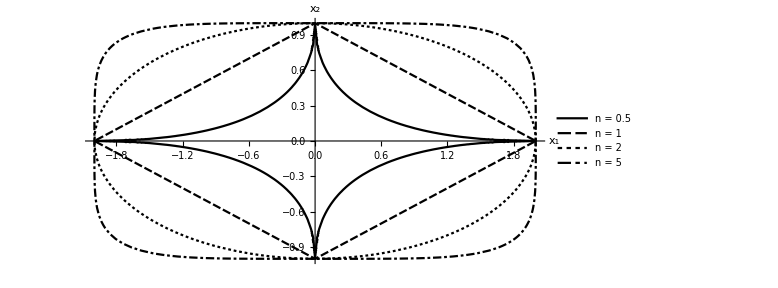

```mathematica
r1=2;r2=1;
n1=0.5;n2=1;n3=2;n4=5;
(*Export["SuperEllipse.svg",*)
ContourPlot[
{ρ[x1,x2,r1,r2,n1]==1,ρ[x1,x2,r1,r2,n2]==1,ρ[x1,x2,r1,r2,n3]==1,ρ[x1,x2,r1,r2,n4]==1},{x1,-r1,r1},{x2,-r2,r2},
Axes->True,Frame->False,AspectRatio->Automatic,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","x_2"},
PlotLegends->{"n = "<>ToString[n1],"n = "<>ToString[n2],"n = "<>ToString[n3],"n = "<>ToString[n4]}
]
```

```mathematica
]
```

```mathematica
FS=26;
r1=1;r2=1;n=2;q=1;
p1=1;p2=2;p3=5;p4=50;
(*Export["PolynomialInfluenceP.pdf",*)
Show[
Plot[
{
φP[x1,0,r1,r2,n,p1,q],
φP[x1,0,r1,r2,n,p2,q],
φP[x1,0,r1,r2,n,p3,q],
φP[x1,0,r1,r2,n,p4,q]},{x1,-1,1},
ImageSize->Large,PlotRange->Full,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"x'_1","φ_(p, q)^P"},
PlotLabels->{
Callout["p = "<>ToString[p1],{Scaled[0.6],Above},CalloutMarker->"Arrow"],
Callout["p = "<>ToString[p2],{Scaled[0.65],Above},CalloutMarker->"Arrow"],
Callout["p = "<>ToString[p3],{Scaled[0.8],Above},CalloutMarker->"Arrow"],
Callout["p = "<>ToString[p4],{Scaled[0.7],Below},CalloutMarker->"Arrow"]
}
],
Graphics[{
Text[Style["q = "<>ToString[q],FS],Scaled[{0.15,0.95}]],
Text[Style["r_1 = "<>ToString[r1],FS],Scaled[{0.15,0.82}]],
Text[Style["x = 0",FS],Scaled[{0.15,0.69}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
r1=1;r2=1;n=2;p=1;
q1=1;q2=2;q3=3;
(*Export["PolynomialInfluenceQ.pdf",*)
Show[
Plot[
{φP[x1,0,r1,r2,n,p,q1],
φP[x1,0,r1,r2,n,p,q2],
φP[x1,0,r1,r2,n,p,q3]},{x1,-1,1},
ImageSize->Large,PlotRange->Full,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"x'_1","φ_(p, q)^P"},
PlotLabels->{
Callout["q = "<>ToString[q1],{Scaled[0.85],Above},CalloutMarker->"Arrow"],
Callout["q = "<>ToString[q2],{Scaled[0.7],Above},CalloutMarker->"Arrow"],
Callout["q = "<>ToString[q3],{Scaled[0.7],Above},CalloutMarker->"Arrow"]
}
],
Graphics[{
Text[Style["p = "<>ToString[p],FS],Scaled[{0.15,0.95}]],
Text[Style["r_1 = "<>ToString[r1],FS],Scaled[{0.15,0.82}]],
Text[Style["x = 0",FS],Scaled[{0.15,0.69}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
r1=1;r2=1;n=2;q=1;
p1=1;p2=1.3;p3=2;p4=10;
(*Export["ExponentialInfluenceP.pdf",*)
Show[
Plot[
{φE[x1,0,r1,r2,n,p1,q],
φE[x1,0,r1,r2,n,p2,q],
φE[x1,0,r1,r2,n,p3,q],
φE[x1,0,r1,r2,n,p4,q]},{x1,-3,3},
ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"x'_1","φ_(p, q)^E"},
PlotLabels->{
Callout["p = "<>ToString[p1],{Scaled[0.635],Above},CalloutMarker->"Arrow"],
Callout["p = "<>ToString[p2],{Scaled[0.61],Above},CalloutMarker->"Arrow"],
Callout["p = "<>ToString[p3],{Scaled[0.61],Above},CalloutMarker->"Arrow"],
Callout["p = "<>ToString[p4],{Scaled[0.635],Above},CalloutMarker->"Arrow"]
}
],
Graphics[{
Text[Style["q = "<>ToString[q],FS],Scaled[{0.15,0.95}]],
Text[Style["r_1 = "<>ToString[r1],FS],Scaled[{0.15,0.82}]],
Text[Style["x = 0",FS],Scaled[{0.15,0.69}]]
}]
]
```

General::munfl: Exp[-59024.9] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
r1=1;r2=1;n=2;p=1;
q1=1;q2=2;q3=3;
(*Export["ExponentialInfluenceQ.pdf",*)
Show[
Plot[
{φE[x1,0,r1,r2,n,p,q1],
φE[x1,0,r1,r2,n,p,q2],
φE[x1,0,r1,r2,n,p,q3]},{x1,-3,3},
ImageSize->Large,PlotRange->Full,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"x'_1","φ_(p, q)^E"},
PlotLabels->{
Callout["q = "<>ToString[q1],{Scaled[0.55],Above},CalloutMarker->"Arrow"],
Callout["q = "<>ToString[q2],{Scaled[0.57],Above},CalloutMarker->"Arrow"],
Callout["q = "<>ToString[q3],{Scaled[0.58],Above},CalloutMarker->"Arrow"]
}
],
Graphics[{
Text[Style["p = "<>ToString[p],FS],Scaled[{0.15,0.95}]],
Text[Style["r_1 = "<>ToString[r1],FS],Scaled[{0.15,0.82}]],
Text[Style["x = 0",FS],Scaled[{0.15,0.69}]]
}]
]
```

-Graphics-

# Конечно - элементная сетка

```mathematica
CS=0.1;
quadratures[poly_]:=Block[{p=poly},
centroid=RegionCentroid[p];
coords=MeshCoordinates[poly];
g[x_]:=(x+centroid)/2;
res=Map[g,coords]
];
points={
(*Boundary*)
{1.7,4},{1.7,5},{2,6},{3,6.7},{4,7},{5,6.6},{6,6.4},{7,6.4},{8,7},{9,7.4},{10,8},{11,8.3},{12,8},{12.5,7},{12.3,6},{12,5},{11.5,4},{11,3.5},{10,2.8},{9,2.5},{8,2.2},{7,2.3},{6,2.1},{5,2},{4,1.9},{3,2.4},{1.8,3},
(*Inner*)
{2.5,4},{2.7,5},{3.5,5.7},{3.8,3.8},{4.2,4.8},{4.4,5.7},{4.2,3.8},{4.8,4.5},{5.3,5.3},{5.2,3.5},{6,4.4},{6.5,5.2},{6.6,3.4},{6.8,4.3},{7.4,5.1},{8,3.3},{8,4.1},{8.9,3.5},{8.8,4.7},{8.3,5.6},{10,4},{9.6,5},{9,6},{10.7,4.8},{10.1,6},{10,6.8},{11.1,5.9},{11.3,7}
};
Boundary=Line[points⟦1;;27⟧];
Msh=
{
Polygon[{points⟦1⟧,points⟦27⟧,points⟦28⟧}],
Polygon[{points⟦1⟧,points⟦2⟧,points⟦29⟧,points⟦28⟧}],
Polygon[{points⟦2⟧,points⟦3⟧,points⟦29⟧}],
Polygon[{points⟦3⟧,points⟦4⟧,points⟦30⟧,points⟦29⟧}],
Polygon[{points⟦4⟧,points⟦5⟧,points⟦30⟧}],
Polygon[{points⟦27⟧,points⟦28⟧,points⟦31⟧,points⟦26⟧}],
Polygon[{points⟦28⟧,points⟦29⟧,points⟦32⟧,points⟦31⟧}],
Polygon[{points⟦29⟧,points⟦30⟧,points⟦33⟧,points⟦32⟧}],
Polygon[{points⟦30⟧,points⟦5⟧,points⟦6⟧}],
Polygon[{points⟦30⟧,points⟦6⟧,points⟦33⟧}],
Polygon[{points⟦26⟧,points⟦31⟧,points⟦34⟧,points⟦25⟧}],
Polygon[{points⟦31⟧,points⟦32⟧,points⟦35⟧,points⟦34⟧}],
Polygon[{points⟦32⟧,points⟦33⟧,points⟦36⟧,points⟦35⟧}],
Polygon[{points⟦33⟧,points⟦6⟧,points⟦36⟧}],
Polygon[{points⟦6⟧,points⟦7⟧,points⟦36⟧}],
Polygon[{points⟦25⟧,points⟦34⟧,points⟦37⟧,points⟦24⟧}],
Polygon[{points⟦34⟧,points⟦35⟧,points⟦38⟧,points⟦37⟧}],
Polygon[{points⟦35⟧,points⟦36⟧,points⟦39⟧,points⟦38⟧}],
Polygon[{points⟦36⟧,points⟦7⟧,points⟦8⟧,points⟦39⟧}],
Polygon[{points⟦24⟧,points⟦37⟧,points⟦23⟧}],
Polygon[{points⟦37⟧,points⟦40⟧,points⟦23⟧}],
Polygon[{points⟦37⟧,points⟦38⟧,points⟦41⟧,points⟦40⟧}],
Polygon[{points⟦38⟧,points⟦39⟧,points⟦42⟧,points⟦41⟧}],
Polygon[{points⟦39⟧,points⟦8⟧,points⟦42⟧}],
Polygon[{points⟦23⟧,points⟦40⟧,points⟦22⟧}],
Polygon[{points⟦22⟧,points⟦40⟧,points⟦43⟧,points⟦21⟧}],
Polygon[{points⟦40⟧,points⟦44⟧,points⟦43⟧}],
Polygon[{points⟦40⟧,points⟦41⟧,points⟦44⟧}],
Polygon[{points⟦41⟧,points⟦42⟧,points⟦44⟧}],
Polygon[{points⟦44⟧,points⟦42⟧,points⟦47⟧,points⟦46⟧}],
Polygon[{points⟦42⟧,points⟦8⟧,points⟦9⟧,points⟦47⟧}],
Polygon[{points⟦21⟧,points⟦43⟧,points⟦45⟧,points⟦20⟧}],
Polygon[{points⟦43⟧,points⟦44⟧,points⟦46⟧,points⟦45⟧}],
Polygon[{points⟦20⟧,points⟦45⟧,points⟦48⟧,points⟦19⟧}],
Polygon[{points⟦45⟧,points⟦46⟧,points⟦49⟧,points⟦48⟧}],
Polygon[{points⟦46⟧,points⟦47⟧,points⟦50⟧,points⟦49⟧}],
Polygon[{points⟦47⟧,points⟦9⟧,points⟦10⟧,points⟦50⟧}],
Polygon[{points⟦19⟧,points⟦48⟧,points⟦18⟧}],
Polygon[{points⟦18⟧,points⟦48⟧,points⟦51⟧,points⟦17⟧}],
Polygon[{points⟦48⟧,points⟦49⟧,points⟦51⟧}],
Polygon[{points⟦49⟧,points⟦50⟧,points⟦53⟧,points⟦52⟧}],
Polygon[{points⟦50⟧,points⟦10⟧,points⟦11⟧,points⟦53⟧}],
Polygon[{points⟦17⟧,points⟦51⟧,points⟦16⟧}],
Polygon[{points⟦51⟧,points⟦54⟧,points⟦15⟧,points⟦16⟧}],
Polygon[{points⟦49⟧,points⟦52⟧,points⟦54⟧,points⟦51⟧}],
Polygon[{points⟦54⟧,points⟦55⟧,points⟦14⟧,points⟦15⟧}],
Polygon[{points⟦52⟧,points⟦53⟧,points⟦55⟧,points⟦54⟧}],
Polygon[{points⟦55⟧,points⟦13⟧,points⟦14⟧}],
Polygon[{points⟦55⟧,points⟦12⟧,points⟦13⟧}],
Polygon[{points⟦53⟧,points⟦11⟧,points⟦12⟧,points⟦55⟧}]
};
```

```mathematica
Bound=BSplineCurve[points⟦1;;27⟧,SplineClosed->True];
FS=38;
nPoints=100; (*количество точек для аппроксимации*)
BoundFunc=BSplineFunction[points⟦1;;27⟧,SplineClosed->True];
curvePoints=Table[BoundFunc[t],{t,0,1,1/nPoints}];
bsplinePolygon=Polygon[curvePoints];
bsplineRegion=BoundaryDiscretizeRegion[bsplinePolygon];
diskRegion=BoundaryDiscretizeRegion[Disk[{8,6},2]];
intersection=RegionIntersection[bsplineRegion,diskRegion];
(*Export["nonlocal_area.svg",*)
Show[
Graphics[{Bound},ImageSize->Large],
RegionPlot[intersection,PlotStyle->LightGray,BoundaryStyle->Black],
Graphics[{
Thickness[0.005],Circle[{8,6},2],
Arrow[{{8,6},{8+2 Cos[π/6],6+2Sin[π/6]}}],
Text[Style["r",FS,FontFamily->"Times",Italic],{9.2,7.1}],
Text[Style["x",FS,FontFamily->"Times",Italic],{8,6.4}],
Text[Style["S'(x)",FS,FontFamily->"Times",Italic],{7.5,5.3}],
Text[Style["S",FS,FontFamily->"Times",Italic],{3,6}]
},ImageSize->Large]
]
```

-Graphics-

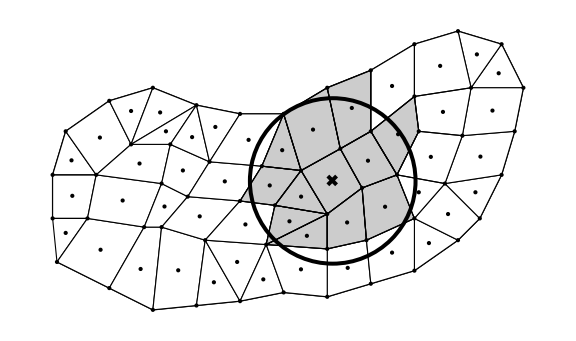

```mathematica
centers=Map[RegionCentroid,Msh];
NLCenter=centers⟦30⟧;
Cros=
{
Line[{{NLCenter⟦1⟧-CS,NLCenter⟦2⟧-CS},{NLCenter⟦1⟧+CS,NLCenter⟦2⟧+CS}}],
Line[{{NLCenter⟦1⟧-CS,NLCenter⟦2⟧+CS},{NLCenter⟦1⟧+CS,NLCenter⟦2⟧-CS}}]
};
NonlocalRadius=Circle[centers⟦30⟧,1.9];
NonlocalArea={Msh⟦23⟧,Msh⟦24⟧,Msh⟦27⟧,Msh⟦28⟧,Msh⟦29⟧,Msh⟦30⟧,Msh⟦31⟧,Msh⟦33⟧,Msh⟦35⟧,Msh⟦36⟧,Msh⟦37⟧,Msh⟦41⟧};
(*Export["ApproxSE.pdf",*)
Graphics[{Boundary,EdgeForm[Directive[Black]],White,Msh,Black,PointSize[Medium],Point[points],Point[centers],Thickness[0.005], NonlocalRadius,Thickness[0.005],Cros,Opacity[0.2],NonlocalArea},ImageSize->Large]
```

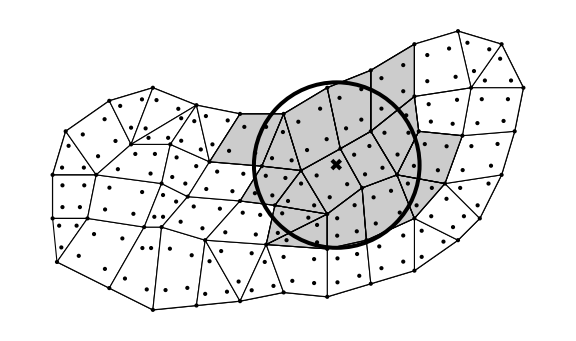

```mathematica
quads=Flatten[Map[Point,Map[quadratures,Msh],{2}],1];
NLCenter=MeshCoordinates[quads⟦106⟧]⟦1⟧;
Cros=
{
Line[{{NLCenter⟦1⟧-CS,NLCenter⟦2⟧-CS},{NLCenter⟦1⟧+CS,NLCenter⟦2⟧+CS}}],
Line[{{NLCenter⟦1⟧-CS,NLCenter⟦2⟧+CS},{NLCenter⟦1⟧+CS,NLCenter⟦2⟧-CS}}]
};
NonlocalRadius=Circle[NLCenter,1.9];
NonlocalArea={Msh⟦19⟧,Msh⟦23⟧,Msh⟦24⟧,Msh⟦27⟧,Msh⟦28⟧,Msh⟦29⟧,Msh⟦30⟧,Msh⟦31⟧,Msh⟦33⟧,Msh⟦35⟧,Msh⟦36⟧,Msh⟦37⟧,Msh⟦40⟧,Msh⟦41⟧,Msh⟦42⟧,Msh⟦45⟧};
(*Export["ApproxSQ.pdf",*)
Graphics[{Boundary,EdgeForm[Directive[Black]],White,Msh,Black,PointSize[Medium],Point[points],quads,Thickness[0.005], NonlocalRadius,Thickness[0.005],Cros,Opacity[0.2],NonlocalArea},ImageSize->Large]
```

```mathematica
a=Min[{{1.7,4},{1.7,5},{2,6},{3,6.7},{4,7},{5,6.6},{6,6.4},{7,6.4},{8,7},{9,7.4},{10,8},{11,8.3},{12,8},{12.5,7},{12.3,6},{12,5},{11.5,4},{11,3.5},{10,2.8},{9,2.5},{8,2.2},{7,2.3},{6,2.1},{5,2},{4,1.9},{3,2.4},{1.8,3}}⟦All,2⟧]
```

1.9

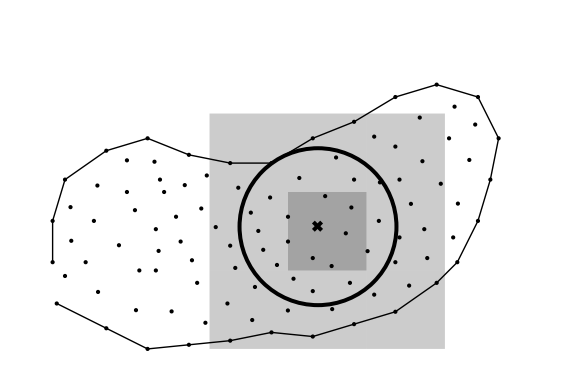

```mathematica
centers=Map[RegionCentroid,Msh];
NLCenter=centers⟦30⟧;
Cros=
{
Line[{{NLCenter⟦1⟧-CS,NLCenter⟦2⟧-CS},{NLCenter⟦1⟧+CS,NLCenter⟦2⟧+CS}}],
Line[{{NLCenter⟦1⟧-CS,NLCenter⟦2⟧+CS},{NLCenter⟦1⟧+CS,NLCenter⟦2⟧-CS}}]
};
r=1.9;
NonlocalRadius=Circle[centers⟦30⟧,r];
NonlocalArea={Msh⟦23⟧,Msh⟦24⟧,Msh⟦27⟧,Msh⟦28⟧,Msh⟦29⟧,Msh⟦30⟧,Msh⟦31⟧,Msh⟦33⟧,Msh⟦35⟧,Msh⟦36⟧,Msh⟦37⟧,Msh⟦41⟧};
cells=Table[Rectangle[{x+1.7,y},{x+1.7+r,y+r}],{x,0,1.9*5,1.9},{y,1.9,1.9*4,1.9}];
nonlocalArea=Table[Rectangle[{x+1.7,y},{x+1.7+r,y+r}],{x,1.9*2,1.9*4,1.9},{y,1.9,1.9*3,1.9}];
(*Export["SearchNeighbours.pdf",*)
Graphics[{Boundary,EdgeForm[Directive[Black]],Transparent,Msh,cells,Opacity[1],Black,PointSize[Medium],Point[points],Point[centers],Thickness[0.005], NonlocalRadius,Thickness[0.005],Cros,
Opacity[0.2],Rectangle[{1.7+1.9 3,1.9 2},{1.7+1.9 3+r,1.9 2+r}],nonlocalArea
},ImageSize->Large]
```

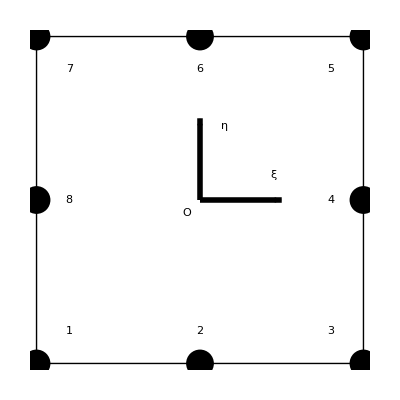

```mathematica
(*Export["QuadraticSerendipity.pdf",*)
Graphics[{
Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}],
PointSize[0.05],Point[{-1,-1}],Point[{0,-1}],Point[{1,-1}],Point[{1,0}],Point[{1,1}],Point[{0,1}],Point[{-1,1}],Point[{-1,0}],
Text[Style[1,Large],{-0.8,-0.8}],Text[Style[2,Large],{0,-0.8}],Text[Style[3,Large],{0.8,-0.8}],Text[Style[4,Large],{0.8,0}],Text[Style[5,Large],{0.8,0.8}],Text[Style[6,Large],{0,0.8}],Text[Style[7,Large],{-0.8,0.8}],Text[Style[8,Large],{-0.8,0}],
Thickness[0.01],Arrow[{{0,0},{0.5,0}}],Arrow[{{0,0},{0,0.5}}],
Text[Style[ξ,Large],{0.45,0.15}],Text[Style[η,Large],{0.15,0.45}],
Text[Style["O", Large], {-0.08, -0.08}]
}]
```

# Задачи на квадратной области

```mathematica
thermallocal=Import["data/Square/thermal/local/solution_thermal_stationary_2d.csv"];
thermalr005p05=Import["data/Square/thermal/r005p05/solution_thermal_stationary_2d.csv"];
thermalr01p05=Import["data/Square/thermal/r01p05/solution_thermal_stationary_2d.csv"];
thermalr015p05=Import["data/Square/thermal/r015p05/solution_thermal_stationary_2d.csv"];
thermalr01p075=Import["data/Square/thermal/r01p075/solution_thermal_stationary_2d.csv"];
thermalr01p025=Import["data/Square/thermal/r01p025/solution_thermal_stationary_2d.csv"];
```

```mathematica
Tlocal=Interpolation[thermallocal⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
Tr005p05=Interpolation[thermalr005p05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
Tr01p05=Interpolation[thermalr01p05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
Tr015p05=Interpolation[thermalr015p05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
Tr01p075=Interpolation[thermalr01p075⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
Tr01p025=Interpolation[thermalr01p025⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
maxTLocal=Abs[Tlocal[0.5,0]];
```

```mathematica
Fylocal=Interpolation[thermallocal⟦2;;All,{1,2,5}⟧,InterpolationOrder->1];
Fyr005p05=Interpolation[thermalr005p05⟦2;;All,{1,2,5}⟧,InterpolationOrder->1];
Fyr01p05=Interpolation[thermalr01p05⟦2;;All,{1,2,5}⟧,InterpolationOrder->1];
Fyr015p05=Interpolation[thermalr015p05⟦2;;All,{1,2,5}⟧,InterpolationOrder->1];
Fyr01p075=Interpolation[thermalr01p075⟦2;;All,{1,2,5}⟧,InterpolationOrder->1];
Fyr01p025=Interpolation[thermalr01p025⟦2;;All,{1,2,5}⟧,InterpolationOrder->1];
```

```mathematica
mechanicallocal=Import["data/Square/mechanical/local/solution_mechanical_2d.csv"];
mechanicalr005p05=Import["data/Square/mechanical/r005_p05/solution_mechanical_2d.csv"];
mechanicalr01p05=Import["data/Square/mechanical/r01_p05/solution_mechanical_2d.csv"];
mechanicalr015p05=Import["data/Square/mechanical/r015_p05/solution_mechanical_2d.csv"];
mechanicalr01p075=Import["data/Square/mechanical/r01_p075/solution_mechanical_2d.csv"];
mechanicalr01p025=Import["data/Square/mechanical/r01_p025/solution_mechanical_2d.csv"];
```

```mathematica
u1local=Interpolation[mechanicallocal⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
u1r005p05=Interpolation[mechanicalr005p05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
u1r01p05=Interpolation[mechanicalr01p05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
u1r015p05=Interpolation[mechanicalr015p05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
u1r01p075=Interpolation[mechanicalr01p075⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
u1r01p025=Interpolation[mechanicalr01p025⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
maxU1Local=Abs[u1local[0.5,0]];
```

```mathematica
σ12local=Interpolation[mechanicallocal⟦2;;All,{1,2,10}⟧,InterpolationOrder->1];
σ12r005p05=Interpolation[mechanicalr005p05⟦2;;All,{1,2,10}⟧,InterpolationOrder->1];
σ12r01p05=Interpolation[mechanicalr01p05⟦2;;All,{1,2,10}⟧,InterpolationOrder->1];
σ12r015p05=Interpolation[mechanicalr015p05⟦2;;All,{1,2,10}⟧,InterpolationOrder->1];
σ12r01p075=Interpolation[mechanicalr01p075⟦2;;All,{1,2,10}⟧,InterpolationOrder->1];
σ12r01p025=Interpolation[mechanicalr01p025⟦2;;All,{1,2,10}⟧,InterpolationOrder->1];
```

```mathematica
opts=Function[{dat,x,y,z},{
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1",dat},
PlotLabels->{
Callout[x,{Scaled[0.6],Above},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->2],
Callout[y,{Scaled[0.76],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->0],
Callout[z,{Scaled[0.93],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->7]
}
}];
text=Function[{x,y,z},{
Text[Style[x,FS],Scaled[{0.2,0.9}]],
Text[Style[y,FS],Scaled[{0.2,0.78}]],
Text[Style[z,FS],Scaled[{0.2,0.66}]]
}];
```

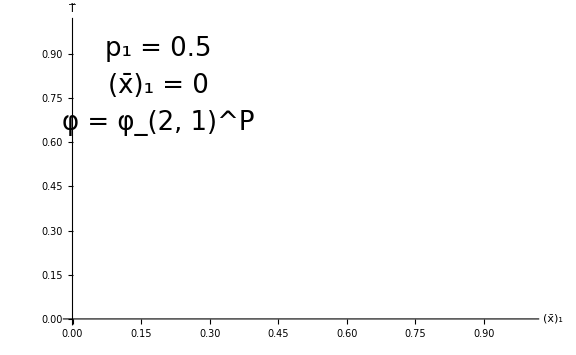

```mathematica
(*Export["TVarR.pdf",*)
Show[
Plot[{(Tr005p05[x,0]-Tlocal[x,0])/maxLocal,(Tr01p05[x,0]-Tlocal[x,0])/maxLocal,(Tr015p05[x,0]-Tlocal[x,0])/maxLocal},{x,-0.5,0.5},Evaluate[opts["T̃","r̄ = 0.05","r̄ = 0.1","r̄ = 0.15"]]],
Graphics[text["p_1 = 0.5","(x̄)_1 = 0","φ = φ_(2, 1)^P"]]
]
```

```mathematica
(*Export["TVarP1.pdf",*)
Show[
Plot[{(Tr01p075[x,0]-Tlocal[x,0])/maxTLocal,(Tr01p05[x,0]-Tlocal[x,0])/maxTLocal,(Tr01p025[x,0]-Tlocal[x,0])/maxTLocal},{x,-0.5,0.5},Evaluate[opts["T̃","p_1 = 0.75","p_1 = 0.5","p_1 = 0.25"]]],
Graphics[text["r̄ = 0.1","(x̄)_1 = 0","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["TVarX2.pdf",*)
Show[
Plot[{(Tr01p05[x,0]-Tlocal[x,0])/maxTLocal,(Tr01p05[x,0.35]-Tlocal[x,0.35])/maxTLocal,(Tr01p05[x,0.5]-Tlocal[x,0.5])/maxTLocal},{x,-0.5,0.5},Evaluate[opts["T̃","(x̄)_2 = 0","(x̄)_2 = 0.35","(x̄)_2 = 0.5"]]],
Graphics[text["p_1 = 0.5","r̄ = 0.1","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["U1VarR.pdf",*)
Show[
Plot[{(u1r005p05[x,0]-u1local[x,0])/maxU1Local,(u1r01p05[x,0]-u1local[x,0])/maxU1Local,(u1r015p05[x,0]-u1local[x,0])/maxU1Local},{x,-0.5,0.5},Evaluate[opts["(ũ)_1","r̄ = 0.05","r̄ = 0.1","r̄ = 0.15"]]],
Graphics[text["p_1 = 0.5","(x̄)_1 = 0","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["U1VarP1.pdf",*)
Show[
Plot[{(u1r01p075[x,0]-u1local[x,0])/maxU1Local,(u1r01p05[x,0]-u1local[x,0])/maxU1Local,(u1r01p025[x,0]-u1local[x,0])/maxU1Local},{x,-0.5,0.5},Evaluate[opts["(ũ)_1","p_1 = 0.75","p_1 = 0.5","p_1 = 0.25"]]],
Graphics[text["r̄ = 0.1","(x̄)_1 = 0","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["U1VarX2.pdf",*)
Show[
Plot[{(u1r01p05[x,0]-u1local[x,0])/maxU1Local,(u1r01p05[x,0.35]-u1local[x,0.35])/maxU1Local,(u1r01p05[x,0.5]-u1local[x,0.5])/maxU1Local},{x,-0.5,0.5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","(ũ)_1"},
PlotLabels->{
Callout["(x̄)_2 = 0",{Scaled[0.8],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->-1],
Callout["(x̄)_2 = 0.35",{Scaled[0.8],Left},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["(x̄)_2 = 0.5",{Scaled[0.91],Left},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->0]
}],
Graphics[text["p_1 = 0.5","r̄ = 0.1","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
FS=32;
FluxAndStress=Function[{f,val,r},
Show[
ContourPlot[f[x,y],{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->Full,
ImageSize->Large,PlotRange->Full,ColorFunction->"GrayTones",ColorFunctionScaling->True,Frame->False,Axes->True,
PlotLegends->BarLegend[Automatic,9,LegendLabel->val],Ticks->{{-0.5,-0.25,0,0.25,0.5},{-0.5,-0.25,0,0.25,0.5}},
LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","(x̄)_2"},Contours->16,ContourStyle->Black],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.5,0.65}]],
Text[Style[r,FS],Scaled[{0.53,0.55}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.515,0.45}]]
}]
]];
```

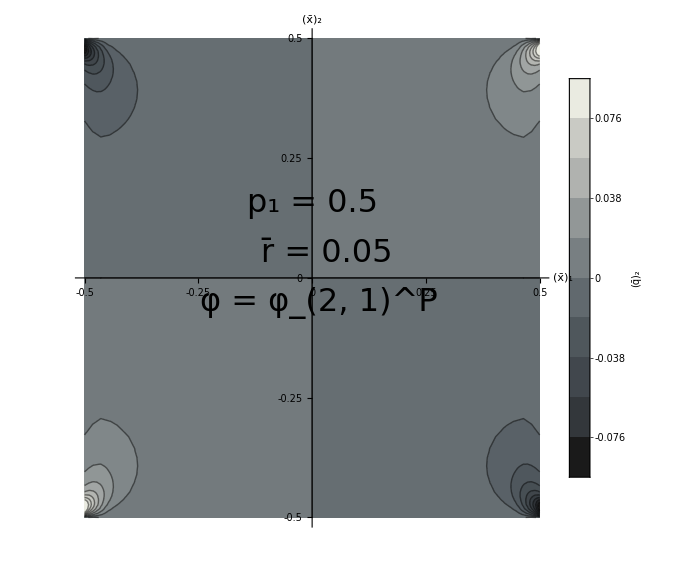

```mathematica
(*Export["Flux2R005.pdf",*)FluxAndStress[Fyr005p05,"(q̄)_2","r̄ = 0.05"](*];
Export["Flux2R015.pdf",FluxAndStress[Fyr015p05,"(q̄)_2","r̄ = 0.15"]];
Export["Sigma12R005.pdf",FluxAndStress[σ12r005p05,"(σ̄)_12","r̄ = 0.05"]];
Export["Sigma12R015.pdf",FluxAndStress[σ12r015p05,"(σ̄)_12","r̄ = 0.15"]];*)
```

```mathematica
thermallocal=Import["data/Square/thermal/local/solution_thermal_stationary_2d.csv"];
thermalconst=Import["data/Square/thermal/const/solution_thermal_stationary_2d.csv"];
thermalN2P1Q1=Import["data/Square/thermal/N2P1Q1/solution_thermal_stationary_2d.csv"];
thermalN2P5Q1=Import["data/Square/thermal/N2P5Q1/solution_thermal_stationary_2d.csv"];
thermalN2P15Q1=Import["data/Square/thermal/N2P15Q1/solution_thermal_stationary_2d.csv"];
thermalN2P1Q3=Import["data/Square/thermal/N2P1Q3/solution_thermal_stationary_2d.csv"];
thermalN2P1Q10=Import["data/Square/thermal/N2P1Q10/solution_thermal_stationary_2d.csv"];
thermalN1P1Q1=Import["data/Square/thermal/N1P1Q1/solution_thermal_stationary_2d.csv"];
thermalN2P1Q1=Import["data/Square/thermal/N2P1Q1/solution_thermal_stationary_2d.csv"];
thermalNinfP1Q1=Import["data/Square/thermal/NinfP1Q1/solution_thermal_stationary_2d.csv"];
```

```mathematica
Tlocal=Interpolation[thermallocal⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
Tconst=Interpolation[thermalconst⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TN2P1Q1=Interpolation[thermalN2P1Q1⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TN2P5Q1=Interpolation[thermalN2P5Q1⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TN2P15Q1=Interpolation[thermalN2P15Q1⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TN2P1Q3=Interpolation[thermalN2P1Q3⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TN2P1Q10=Interpolation[thermalN2P1Q10⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TN1P1Q1=Interpolation[thermalN1P1Q1⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TN2P1Q1=Interpolation[thermalN2P1Q1⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TNinfP1Q1=Interpolation[thermalNinfP1Q1⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TMax=Abs[Tlocal[0.5,0]];
```

```mathematica
(*Export["TPolyInfluenceVariationP.pdf",*)
Show[
Plot[{(TN2P1Q1[x,0.5]+x)/TMax,(TN2P5Q1[x,0.5]+x)/TMax,(Tconst[x,0.5]+x)/TMax},{x,-0.5,0.5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","T̃"},
PlotLabels->{
Callout["p = 1",{Scaled[0.75],Above},CalloutMarker->"Arrow",Background->Transparent],
Callout["p = 5",{Scaled[0.8],Right},CalloutMarker->"Arrow",Background->Transparent],
Callout["p = ∞",{Scaled[0.92],Right},CalloutMarker->"Arrow",Background->Transparent]
}],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.1}]],
Text[Style["r̄ = 0.1",FS],Scaled[{0.2,0.22}]],
Text[Style["(x̄)_2 = 0.5",FS],Scaled[{0.2,0.34}]],
Text[Style["q = 1",FS],Scaled[{0.2,0.95}]],
Text[Style["n = 2",FS],Scaled[{0.2,0.83}]]
}]
]
```

-Graphics-

```mathematica
(*Export["TPolyInfluenceVariationQ.pdf",*)
Show[
Plot[{(TN2P1Q1[x,0.5]+x)/TMax,(TN2P1Q3[x,0.5]+x)/TMax,(TN2P1Q10[x,0.5]+x)/TMax},{x,-0.5,0.5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","T̃"},
PlotLabels->{
Callout["q = 1",{Scaled[0.93],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->2],
Callout["q = 3",{Scaled[0.8],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["q = 10",{Scaled[0.8],Left},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->7]
}],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.1}]],
Text[Style["r̄ = 0.1",FS],Scaled[{0.2,0.22}]],
Text[Style["(x̄)_2 = 0.5",FS],Scaled[{0.2,0.34}]],
Text[Style["p = 1",FS],Scaled[{0.2,0.95}]],
Text[Style["n = 2",FS],Scaled[{0.2,0.83}]]
}]
]
```

-Graphics-

```mathematica
(*Export["TPolyInfluenceVariationN.pdf",*)
Show[
Plot[{(TN1P1Q1[x,0.5]+x)/TMax,(TN2P1Q1[x,0.5]+x)/TMax,(TNinfP1Q1[x,0.5]+x)/TMax},{x,-0.5,0.5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","T̃"},
PlotLabels->{
Callout["n = 1",{Scaled[0.8],Above},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->2],
Callout["n = 2",{Scaled[0.8],Right},CalloutMarker->"Arrow",FrameMargins->0],
Callout["n = ∞",{Scaled[0.93],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1]
}],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.1}]],
Text[Style["r̄ = 0.1",FS],Scaled[{0.2,0.22}]],
Text[Style["(x̄)_2 = 0.5",FS],Scaled[{0.2,0.34}]],
Text[Style["p = 1",FS],Scaled[{0.2,0.95}]],
Text[Style["q = 1",FS],Scaled[{0.2,0.83}]]
}]
]
```

-Graphics-

```mathematica
thermallocal=Import["data/Square/thermal/local/solution_thermal_stationary_2d.csv"];
thermalconst=Import["data/Square/thermal/const/solution_thermal_stationary_2d.csv"];
thermalExpN1P2Q05=Import["data/Square/thermal/ExpN1P2Q05/solution_thermal_stationary_2d.csv"];
thermalExpN2P2Q05=Import["data/Square/thermal/ExpN2P2Q05/solution_thermal_stationary_2d.csv"];
thermalExpNinfP2Q05=Import["data/Square/thermal/ExpNinfP2Q05/solution_thermal_stationary_2d.csv"];
thermalExpN2P1Q1=Import["data/Square/thermal/ExpN2P1Q1/solution_thermal_stationary_2d.csv"];
thermalExpN2P2Q1=Import["data/Square/thermal/ExpN2P2Q1/solution_thermal_stationary_2d.csv"];
thermalExpN2P5Q05=Import["data/Square/thermal/ExpN2P5Q05/solution_thermal_stationary_2d.csv"];
thermalExpN2P2Q3=Import["data/Square/thermal/ExpN2P2Q3/solution_thermal_stationary_2d.csv"];
```

```mathematica
Tlocal=Interpolation[thermallocal⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
Tconst=Interpolation[thermalconst⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TExpN1P2Q05=Interpolation[thermalExpN1P2Q05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TExpN2P2Q05=Interpolation[thermalExpN2P2Q05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TExpNinfP2Q05=Interpolation[thermalExpNinfP2Q05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TExpN2P1Q1=Interpolation[thermalExpN2P1Q1⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TExpN2P2Q1=Interpolation[thermalExpN2P2Q1⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TExpN2P5Q05=Interpolation[thermalExpN2P5Q05⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TExpN2P2Q3=Interpolation[thermalExpN2P2Q3⟦2;;All,{1,2,3}⟧,InterpolationOrder->1];
TMax=Abs[Tlocal[0.5,0]];
```

```mathematica
(*Export["TExpInfluenceVariationP.pdf",*)
Show[
Plot[{(TExpN2P2Q05[x,0.5]+x)/TMax,(TExpN2P5Q05[x,0.5]+x)/TMax,(Tconst[x,0.5]+x)/TMax},{x,-0.5,0.5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","T̃"},
PlotLabels->{
Callout["p = 2, r̄ = 0.033",{Scaled[0.8],Left},CalloutMarker->"Arrow",Background->Transparent],
Callout["p = 5, r̄ = 0.070",{Scaled[0.77],Right},CalloutMarker->"Arrow",Background->Transparent],
Callout["p = ∞, r̄ = 0.1",{Scaled[0.89],Right},CalloutMarker->"Arrow",Background->Transparent]
}],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.15}]],
Text[Style["(x̄)_2 = 0.5",FS],Scaled[{0.2,0.3}]],
Text[Style["q = 0.5",FS],Scaled[{0.2,0.95}]],
Text[Style["n = 2",FS],Scaled[{0.2,0.83}]]
}]
]
```

-Graphics-

```mathematica
(*Export["TExpInfluenceVariationQ.pdf",*)
Show[
Plot[{(TExpN2P2Q05[x,0.5]+x)/TMax,(TExpN2P2Q1[x,0.5]+x)/TMax,(TExpN2P2Q3[x,0.5]+x)/TMax},{x,-0.5,0.5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","T̃"},
PlotLabels->{
Callout["q = 0.5",{Scaled[0.93],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->2],
Callout["q = 1",{Scaled[0.8],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["q = 3",{Scaled[0.8],Left},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->7]
}],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.1}]],
Text[Style["r̄ = 0.033",FS],Scaled[{0.2,0.22}]],
Text[Style["(x̄)_2 = 0.5",FS],Scaled[{0.2,0.34}]],
Text[Style["p = 2",FS],Scaled[{0.2,0.95}]],
Text[Style["n = 2",FS],Scaled[{0.2,0.83}]]
}]
]
```

-Graphics-

```mathematica
(*Export["TExpInfluenceVariationN.pdf",*)
Show[
Plot[{(TExpN1P2Q05[x,0.5]+x)/TMax,(TExpN2P2Q05[x,0.5]+x)/TMax,(TExpNinfP2Q05[x,0.5]+x)/TMax},{x,-0.5,0.5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","T̃"},
PlotLabels->{
Callout["n = 1",{Scaled[0.8],Above},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->2],
Callout["n = 2",{Scaled[0.8],Right},CalloutMarker->"Arrow",FrameMargins->0],
Callout["n = ∞",{Scaled[0.93],Right},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1]
}],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.1}]],
Text[Style["r̄ = 0.033",FS],Scaled[{0.2,0.22}]],
Text[Style["(x̄)_2 = 0.5",FS],Scaled[{0.2,0.34}]],
Text[Style["p = 2",FS],Scaled[{0.2,0.95}]],
Text[Style["q = 0.5",FS],Scaled[{0.2,0.83}]]
}]
]
```

-Graphics-

# Принцип Сен - Венана

```mathematica
f1[x_]:=1;
f2[x_]:=1-2Abs[x];
f3[x_]:=2Abs[x];
```

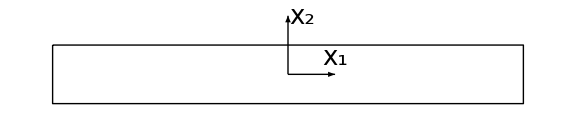

```mathematica
FS=26;
N0=7;
Boundaries:=Function[{f,fiz,fstr,reverse},
{
Arrowheads[0.015],
LeftP=Table[Arrow[{{-5,-0.5+n/N0},{-5-f[-0.5+n/N0],-0.5+n/N0}}],{n,0,N0}],
RightP=Table[Arrow[
If[reverse,
{{5+f[-0.5+n/N0],-0.5+n/N0},{5,-0.5+n/N0}},
{{5,-0.5+n/N0},{5+f[-0.5+n/N0],-0.5+n/N0}}
]
],{n,0,N0}],
σL=Text[Style[fiz<>"=-"<>fstr<>"((x̄)_2)",FS],{-4.4,1}],
σR=Text[Style[fiz<>"="<>fstr<>"((x̄)_2)",FS],{4.5,1}]
}
]
rect=Line[{{-5,0.5},{5,0.5},{5,-0.5},{-5,-0.5},{-5,0.5}}];
axes={
Arrow[{{0,0},{1,0}}],Text[Style["x_1",FS],{1,0.3}],
Arrow[{{0,0},{0,1}}],Text[Style["x_2",FS],{0.3,1}]
};
SaintVenantRect=Graphics[{Thick,rect,Arrowheads[0.02],axes},ImageSize->Large]
```

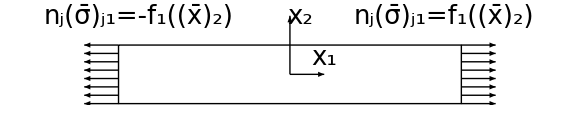

```mathematica
(*Export["RectangleStressF1.pdf",*)
Show[
SaintVenantRect,
Graphics[{Boundaries[f1,"n_j(σ̄)_j1","f_1",False]},ImageSize->Large]
]
```

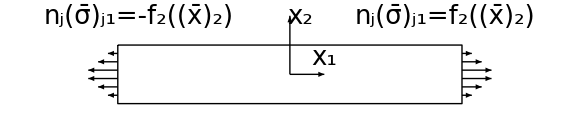

```mathematica
(*Export["RectangleStressF2.pdf",*)
Show[
SaintVenantRect,
Graphics[{Boundaries[f2,"n_j(σ̄)_j1","f_2",False]},ImageSize->Large]
]
```

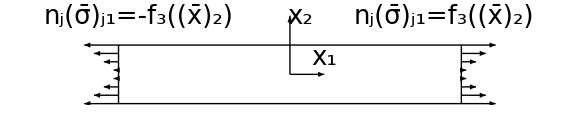

```mathematica
(*Export["RectangleStressF3.pdf",*)
Show[
SaintVenantRect,
Graphics[{Boundaries[f3,"n_j(σ̄)_j1","f_3",False]},ImageSize->Large]
]
```

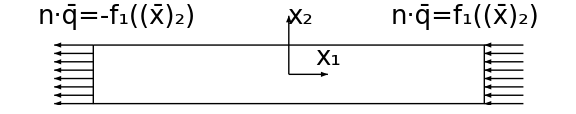

```mathematica
(*Export["RectangleFluxF1.pdf",*)
Show[
SaintVenantRect,
Graphics[{Boundaries[f1,"n·q̄","f_1",True]},ImageSize->Large]
]
```

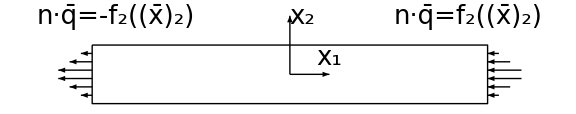

```mathematica
(*Export["RectangleFluxF2.pdf",*)
Show[
SaintVenantRect,
Graphics[{Boundaries[f2,"n·q̄","f_2",True]},ImageSize->Large]
]
```

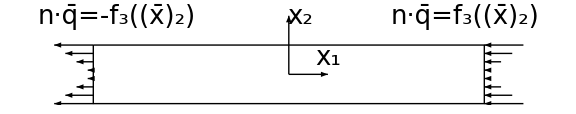

```mathematica
(*Export["RectangleFluxF3.pdf",*)
Show[
SaintVenantRect,
Graphics[{Boundaries[f3,"n·q̄","f_3",True]},ImageSize->Large]
]
```

```mathematica
ThermalDataLocal=Import["data/SaintVenant/Thermal/local/solution_thermal_stationary_2d.csv"];
ThermalDataLocalTriangle=Import["data/SaintVenant/Thermal/local_triangle/solution_thermal_stationary_2d.csv"];
ThermalDataLocalIverseTriangle=Import["data/SaintVenant/Thermal/local_inverse_triangle/solution_thermal_stationary_2d.csv"];
ThermalDatar01p05=Import["data/SaintVenant/Thermal/r01p05/solution_thermal_stationary_2d.csv"];
ThermalDatar01p05Triangle=Import["data/SaintVenant/Thermal/r01p05_triangle/solution_thermal_stationary_2d.csv"];
ThermalDatar01p05TriangleInverse=Import["data/SaintVenant/Thermal/r01p05_inverse_triangle/solution_thermal_stationary_2d.csv"];
```

```mathematica
FxLocal=Interpolation[ThermalDataLocal⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
FxLocalTriangle=Interpolation[ThermalDataLocalTriangle⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
FxLocalTriangleInverse=Interpolation[ThermalDataLocalIverseTriangle⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
Fxr01p05=Interpolation[ThermalDatar01p05⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
Fxr01p05Triangle=Interpolation[ThermalDatar01p05Triangle⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
Fxr01p05TriangleInverse=Interpolation[ThermalDatar01p05TriangleInverse⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
```

```mathematica
FS=26;
opts=Function[{Pos1,Pos2,Pos3,Y,theme},
{PlotRange->Full,ImageSize->Large,PlotTheme->theme,LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1",Y},
PlotLabels->{
Callout["f = f_1",{Scaled[0.75],Pos1},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->-1],
Callout["f = f_2",{Scaled[0.92],Pos2},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->5],
Callout["f = f_3",{Scaled[0.92],Pos3},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->5]
}}
];
text=Function[{x,p,r,phi},{
Text[Style[x,FS],Scaled[{0.25,0.725}]],
Text[Style[p,FS],Scaled[{0.25,0.575}]],
Text[Style[r,FS],Scaled[{0.25,0.425}]],
Text[Style[phi,FS],Scaled[{0.25,0.275}]]
}];
```

```mathematica
(*Export["FluxStabilityX0P1.pdf",*)
Show[
Plot[{1,FxLocalTriangle[x,0],FxLocalTriangleInverse[x,0]},{x,-5,5},Evaluate[opts[Above,Left,Right,"(q̄)_1","Monochrome"]]],
Graphics[text["(x̄)_2 = 0","p_1 = 1","",""]]
]
```

-Graphics-

```mathematica
(*Export["FluxStabilityX05P1.pdf",*)
Show[
Plot[{1,FxLocalTriangle[x,0.5],FxLocalTriangleInverse[x,0.5]},{x,-5,5},Evaluate[opts[Above,Right,Left,"(q̄)_1","Monochrome"]]],
Graphics[text["(x̄)_2 = 0.5","p_1 = 1","",""]]
]
```

-Graphics-

```mathematica
(*Export["FluxStabilityX0P05.pdf",*)
Show[
Plot[{Fxr01p05[x,0],Fxr01p05Triangle[x,0],Fxr01p05TriangleInverse[x,0]},{x,-5,5},Evaluate[opts[Above,Left,Right,"(q̄)_1","Monochrome"]]],
Graphics[text["(x̄)_2 = 0","p_1 = 0.5","r̄ = 0.1","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["FluxStabilityX05P05.pdf",*)
Show[
Plot[{Fxr01p05[x,0.5],Fxr01p05Triangle[x,0.5],Fxr01p05TriangleInverse[x,0.5]},{x,-5,5},Evaluate[opts[Above,Right,Left,"(q̄)_1","Monochrome"]]],
Graphics[text["(x̄)_2 = 0.5","p_1 = 0.5","r̄ = 0.1","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
MechanicalDataLocal=Import["data/SaintVenant/Mechanical/local/solution_mechanical_2d.csv"];
MechanicalDataLocalTriangle=Import["data/SaintVenant/Mechanical/local_triangle/solution_mechanical_2d.csv"];
MechanicalDataLocalIverseTriangle=Import["data/SaintVenant/Mechanical/local_inverse_triangle/solution_mechanical_2d.csv"];
MechanicalDatar01p05=Import["data/SaintVenant/Mechanical/r01p05/solution_mechanical_2d.csv"];
MechanicalDatar01p05Triangle=Import["data/SaintVenant/Mechanical/r01p05_triangle/solution_mechanical_2d.csv"];
MechanicalDatar01p05TriangleInverse=Import["data/SaintVenant/Mechanical/r01p05_inverse_triangle/solution_mechanical_2d.csv"];
```

```mathematica
σ11Local=Interpolation[MechanicalDataLocal⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11LocalTriangle=Interpolation[MechanicalDataLocalTriangle⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11LocalTriangleInverse=Interpolation[MechanicalDataLocalIverseTriangle⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11r01p05=Interpolation[MechanicalDatar01p05⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11r01p05Triangle=Interpolation[MechanicalDatar01p05Triangle⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11r01p05TriangleInverse=Interpolation[MechanicalDatar01p05TriangleInverse⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
```

```mathematica
(*Export["SaintVenantX0P1.pdf",*)
Show[
Plot[{1,σ11LocalTriangle[x,0],σ11LocalTriangleInverse[x,0]},{x,-5,5},Evaluate[opts[Top,Left,Right,"(σ̄)_11","Monochrome"]]],
Graphics[text["(x̄)_2 = 0","p_1 = 1","",""]]
]
```

-Graphics-

```mathematica
(*Export["SaintVenantX05P1.pdf",*)
Show[
Plot[{1,σ11LocalTriangle[x,0.5],σ11LocalTriangleInverse[x,0.5]},{x,-5,5},Evaluate[opts[Top,Right,Left,"(σ̄)_11","Monochrome"]]],
Graphics[text["(x̄)_2 = 0.5","p_1 = 1","",""]]
]
```

-Graphics-

```mathematica
(*Export["SaintVenantX0P05.pdf",*)
Show[
Plot[{σ11r01p05[x,0],σ11r01p05Triangle[x,0],σ11r01p05TriangleInverse[x,0]},{x,-5,5},Evaluate[opts[Top,Left,Right,"(σ̄)_11","Monochrome"]]],
Graphics[text["(x̄)_2 = 0","p_1 = 0.5","r̄ = 0.1","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["SaintVenantX0P05Presentation.pdf",*)
Show[
Plot[{σ11r01p05[x,0],σ11r01p05Triangle[x,0],σ11r01p05TriangleInverse[x,0]},{x,-5,5},Evaluate[opts[Top,Left,Right,"(σ̄)_11","Rainbow"]]],
Graphics[text["(x̄)_2 = 0","p_1 = 0.5","r̄ = 0.1","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["SaintVenantX05P05.pdf",*)
Show[
Plot[{σ11r01p05[x,0.5],σ11r01p05Triangle[x,0.5],σ11r01p05TriangleInverse[x,0.5]},{x,-5,5},Evaluate[opts[Top,Right,Left,"(σ̄)_11","Monochrome"]]],
Graphics[text["(x̄)_2 = 0.5","p_1 = 0.5","r̄ = 0.1","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["SaintVenantX05P05Presentation.pdf",*)
Show[
Plot[{σ11r01p05[x,0.5],σ11r01p05Triangle[x,0.5],σ11r01p05TriangleInverse[x,0.5]},{x,-5,5},Evaluate[opts[Top,Right,Left,"(σ̄)_11","Rainbow"]]],
Graphics[text["(x̄)_2 = 0.5","p_1 = 0.5","r̄ = 0.1","φ = φ_(2, 1)^P"]]
]
```

-Graphics-

```mathematica
(*Export["StabilityLogX0.pdf",*)
Plot[{
Log10[Abs[FxLocal[x,0]-FxLocalTriangle[x,0]]],
Log10[Abs[Fxr01p05[x,0]-Fxr01p05Triangle[x,0]]],
Log10[Abs[σ11Local[x,0]-σ11LocalTriangle[x,0]]],
Log10[Abs[σ11r01p05[x,0]-σ11r01p05Triangle[x,0]]]
},{x,-5,5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","log_10(|𝒮_1-𝒮_2|) ((x̄)_2 = 0)"},
PlotLabels->{
Callout["(q̄)_1^L",{Scaled[0.15],Below},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["(q̄)_1^NL",{Scaled[0.67],Below},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["(σ̄)_11^L",{Scaled[0.45],Top},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["(σ̄)_11^NL",{Scaled[0.55],Top},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1]
}]
```

-Graphics-

```mathematica
(*Export["StabilityLogX05.pdf",*)
Plot[{
Log10[Abs[FxLocal[x,0.5]-FxLocalTriangle[x,0.5]]],
Log10[Abs[Fxr01p05[x,0.5]-Fxr01p05Triangle[x,0.5]]],
Log10[Abs[σ11Local[x,0.5]-σ11LocalTriangle[x,0.5]]],
Log10[Abs[σ11r01p05[x,0.5]-σ11r01p05Triangle[x,0.5]]]
},{x,-5,5},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","log_10(|𝒮_1-𝒮_2|) ((x̄)_2 = 0.5)"},
PlotLabels->{
Callout["(q̄)_1^L",{Scaled[0.2],Below},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["(q̄)_1^NL",{Scaled[0.7],Below},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["(σ̄)_11^L",{Scaled[0.35],Top},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1],
Callout["(σ̄)_11^NL",{Scaled[0.6],Top},CalloutMarker->"Arrow",Background->Transparent,FrameMargins->1]
}]
```

-Graphics-

```mathematica
ThermalDataLocal=Import["data/SaintVenant/Thermal/local/solution_thermal_stationary_2d.csv"];
ThermalDatar005p05=Import["data/SaintVenant/Thermal/r005p05/solution_thermal_stationary_2d.csv"];
ThermalDatar01p075=Import["data/SaintVenant/Thermal/r01p075/solution_thermal_stationary_2d.csv"];
ThermalDatar01p05=Import["data/SaintVenant/Thermal/r01p05/solution_thermal_stationary_2d.csv"];
ThermalDatar01p025=Import["data/SaintVenant/Thermal/r01p025/solution_thermal_stationary_2d.csv"];
ThermalDatar015p05=Import["data/SaintVenant/Thermal/r015p05/solution_thermal_stationary_2d.csv"];
```

```mathematica
FxLocal=Interpolation[ThermalDataLocal⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
Fxr005p05=Interpolation[ThermalDatar005p05⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
Fxr01p075=Interpolation[ThermalDatar01p075⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
Fxr01p05=Interpolation[ThermalDatar01p05⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
Fxr01p025=Interpolation[ThermalDatar01p025⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
Fxr015p05=Interpolation[ThermalDatar015p05⟦2;;All,{1,2,4}⟧,InterpolationOrder->1];
```

```mathematica
FS=26;
(*Export["HeatFluxStabilityVariationR.pdf",*)
Show[
Plot[{1,Fxr005p05[0,y],Fxr01p05[0,y],Fxr015p05[0,y]},{y,-0.5,0.5},ImageSize->Large,PlotRange->Full,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_2","𝒮"},
PlotLabels->{
Callout["r̄ = 0",{Scaled[0.18],Below},Background->Transparent,FrameMargins->-9,CalloutMarker->"Arrow"],
Callout["r̄ = 0.05",{Scaled[0.37],Below},Background->Transparent,FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["r̄ = 0.1",{Scaled[0.58],Below},Background->Transparent,FrameMargins->-1,CalloutMarker->"Arrow"],
Callout["r̄ = 0.15",{Scaled[0.75],Below},Background->Transparent,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p = 0.5",FS],Scaled[{0.25,0.6}]],
Text[Style["(x̄)_1 = 0",FS],Scaled[{0.25,0.45}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.25,0.3}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["HeatFluxStabilityVariationRPresentation.pdf",*)
Show[
Plot[{1,Fxr005p05[0,y],Fxr01p05[0,y],Fxr015p05[0,y]},{y,-0.5,0.5},ImageSize->Large,PlotRange->Full,PlotTheme->"Rainbow",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_2","𝒮"},
PlotLabels->{
Callout["r̄ = 0",{Scaled[0.18],Below},Background->Transparent,FrameMargins->-9,CalloutMarker->"Arrow"],
Callout["r̄ = 0.05",{Scaled[0.37],Below},Background->Transparent,FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["r̄ = 0.1",{Scaled[0.58],Below},Background->Transparent,FrameMargins->-1,CalloutMarker->"Arrow"],
Callout["r̄ = 0.15",{Scaled[0.75],Below},Background->Transparent,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p = 0.5",FS],Scaled[{0.25,0.6}]],
Text[Style["(x̄)_1 = 0",FS],Scaled[{0.25,0.45}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.25,0.3}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["HeatFluxStabilityVariationP1.pdf",*)
Show[
Plot[{1,Fxr01p075[0,y],Fxr01p05[0,y],Fxr01p025[0,y]},{y,-0.5,0.5},ImageSize->Large,PlotRange->Full,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_2","𝒮"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.18],Below},Background->Transparent,FrameMargins->-9,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.39],Below},Background->Transparent,FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.585],Below},Background->Transparent,FrameMargins->-1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.73],Below},Background->Transparent,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["r̄ = 0.1",FS],Scaled[{0.25,0.6}]],
Text[Style["(x̄)_1 = 0",FS],Scaled[{0.25,0.45}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.25,0.3}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["HeatFluxStabilityVariationP1Presentation.pdf",*)
Show[
Plot[{1,Fxr01p075[0,y],Fxr01p05[0,y],Fxr01p025[0,y]},{y,-0.5,0.5},ImageSize->Large,PlotRange->Full,PlotTheme->"Rainbow",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_2","𝒮"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.18],Below},Background->Transparent,FrameMargins->-9,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.39],Below},Background->Transparent,FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.585],Below},Background->Transparent,FrameMargins->-1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.73],Below},Background->Transparent,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["r̄ = 0.1",FS],Scaled[{0.25,0.6}]],
Text[Style["(x̄)_1 = 0",FS],Scaled[{0.25,0.45}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.25,0.3}]]
}]
]
```

-Graphics-

```mathematica
MechDataLocal=Import["data/SaintVenant/Mechanical/local/solution_mechanical_2d.csv"];
MechDatar005p05=Import["data/SaintVenant/Mechanical/r005p05/solution_mechanical_2d.csv"];
MechDatar01p075=Import["data/SaintVenant/Mechanical/r01p075/solution_mechanical_2d.csv"];
MechDatar01p05=Import["data/SaintVenant/Mechanical/r01p05/solution_mechanical_2d.csv"];
MechDatar01p025=Import["data/SaintVenant/Mechanical/r01p025/solution_mechanical_2d.csv"];
MechDatar015p05=Import["data/SaintVenant/Mechanical/r015p05/solution_mechanical_2d.csv"];
```

```mathematica
σ11Local=Interpolation[MechDataLocal⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11r005p05=Interpolation[MechDatar005p05⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11r01p075=Interpolation[MechDatar01p075⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11r01p05=Interpolation[MechDatar01p05⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11r01p025=Interpolation[MechDatar01p025⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
σ11r015p05=Interpolation[MechDatar015p05⟦2;;All,{1,2,8}⟧,InterpolationOrder->1];
```

```mathematica
FS=26;
(*Export["SaintVenantVariationR.pdf",*)
Show[
Plot[{1,σ11r005p05[0,y],σ11r01p05[0,y],σ11r015p05[0,y]},{y,-0.5,0.5},ImageSize->Large,PlotRange->Full,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄')_2","(σ̄)_11"},
PlotLabels->{
Callout["r̄ = 0",{Scaled[0.18],Below},Background->Transparent,FrameMargins->-9,CalloutMarker->"Arrow"],
Callout["r̄ = 0.05",{Scaled[0.37],Below},Background->Transparent,FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["r̄ = 0.1",{Scaled[0.58],Below},Background->Transparent,FrameMargins->-1,CalloutMarker->"Arrow"],
Callout["r̄ = 0.15",{Scaled[0.75],Below},Background->Transparent,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p = 0.5",FS],Scaled[{0.25,0.6}]],
Text[Style["(x̄)_1 = 0",FS],Scaled[{0.25,0.45}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.25,0.3}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["SaintVenantVariationP1.pdf",*)
Show[
Plot[{1,σ11r01p075[0,y],σ11r01p05[0,y],σ11r01p025[0,y]},{y,-0.5,0.5},ImageSize->Large,PlotRange->Full,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄')_2","(σ̄)_11"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.18],Below},Background->Transparent,FrameMargins->-9,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.39],Below},Background->Transparent,FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.585],Below},Background->Transparent,FrameMargins->-1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.73],Below},Background->Transparent,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["r̄ = 0.1",FS],Scaled[{0.25,0.6}]],
Text[Style["(x̄)_1 = 0",FS],Scaled[{0.25,0.45}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.25,0.3}]]
}]
]
```

-Graphics-

# Т - область

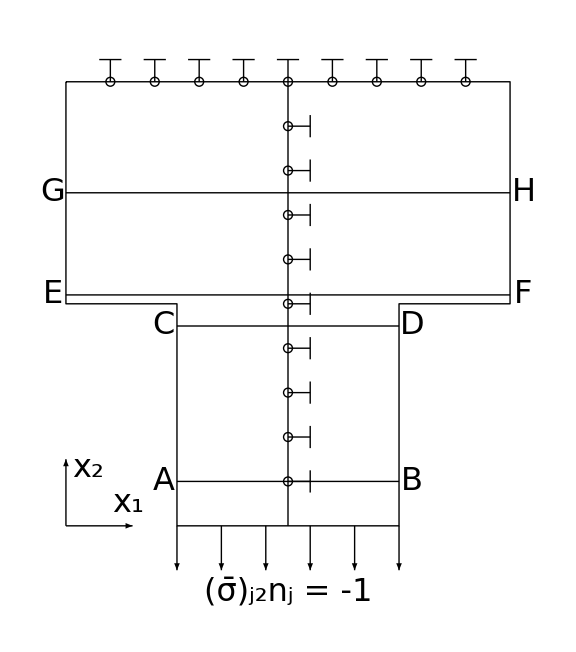

```mathematica
N0=10;
FS=32;
Tarea=Line[{{0,1},{1,1},{1,0.5},{0.75,0.5},{0.75,0},{0.25,0},{0.25,0.5},{0,0.5},{0,1}}];
Symmetry=Line[{{0.5,0},{0.5,1}}];
u1=Table[{Line[{{n/N0,1},{n/N0,1.05}}],Circle[{n/N0,1},0.01],Line[{{n/N0-1/(4N0),1.05},{n/N0+1/(4N0),1.05}}]},{n,1,N0-1}];
u2=Table[{Line[{{0.5,n/N0},{0.55,n/N0}}],Circle[{0.5,n/N0},0.01],Line[{{0.55,n/N0-1/(4N0)},{0.55,n/N0+1/(4N0)}}]},{n,1,N0-1}];
σDown=Table[Arrow[{{n/N0+1/(2N0),0},{n/N0+1/(2N0),-0.1}}],{n,2,N0-3}];
σDownText=Text[Style["(σ̄)_j2n_j = -1",FS],{0.5,-0.15}];
axes={
Arrow[{{0,0},{0.15,0}}],Text[Style["x_1",FS],{0.14,0.05}],
Arrow[{{0,0},{0,0.15}}],Text[Style["x_2",FS],{0.05,0.13}]
};
AB ={Line[{{0.25,0.1},{0.75,0.1}}],Text[Style["A",FS],{0.22,0.1}],Text[Style["B",FS],{0.78,0.1}]};
CD={Line[{{0.25,0.45},{0.75,0.45}}],Text[Style["C",FS],{0.22,0.45}],Text[Style["D",FS],{0.78,0.45}]};
EF={Line[{{0,0.52},{1,0.52}}],Text[Style["E",FS],{-0.03,0.52}],Text[Style["F",FS],{1.03,0.52}]};
GH={Line[{{0,0.75},{1,0.75}}],Text[Style["G",FS],{-0.03,0.75}],Text[Style["H",FS],{1.03,0.75}]};
(*Export["TArea.pdf",*)
Graphics[{Thick,Tarea,Symmetry,u1,u2,σDown,σDownText,axes, AB,CD,EF,GH},ImageSize->Large]
```

```mathematica
Tlocal=Import["data/TShape/LocalStress/Local/solution_mechanical_2d.csv"];
Tr005p05=Import["data/TShape/LocalStress/r005p05/solution_mechanical_2d.csv"];
Tr01p075=Import["data/TShape/LocalStress/r01p075/solution_mechanical_2d.csv"];
Tr01p05=Import["data/TShape/LocalStress/r01p05/solution_mechanical_2d.csv"];
Tr01p025=Import["data/TShape/LocalStress/r01p025/solution_mechanical_2d.csv"];
Tr015p05=Import["data/TShape/LocalStress/r015p05/solution_mechanical_2d.csv"];
```

```mathematica
σ22Local=Interpolation[Tlocal⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
σ22r005p05=Interpolation[Tr005p05⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
σ22r01p075=Interpolation[Tr01p075⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
σ22r01p05=Interpolation[Tr01p05⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
σ22r01p025=Interpolation[Tr01p025⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
σ22r015p05=Interpolation[Tr015p05⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
```

```mathematica
σ22Integral[σ22_]:=Join[
Table[{y,NIntegrate[σ22[x,y],{x,0.25,0.75}]},{y,0,0.5-1/150,1/150}],
Table[{y,NIntegrate[σ22[x,y],{x,0,1}]},{y,0.5+1/150,1,1/150}]
]
```

```mathematica
Off[NIntegrate::ncvb];
Off[NIntegrate::slwcon];
σ22IntegralLocal=Interpolation[σ22Integral[σ22Local],InterpolationOrder->1];
σ22Integralr005p05=Interpolation[σ22Integral[σ22r005p05],InterpolationOrder->1];
σ22Integralr01p075=Interpolation[σ22Integral[σ22r01p075],InterpolationOrder->1];
σ22Integralr01p05=Interpolation[σ22Integral[σ22r01p05],InterpolationOrder->1];
σ22Integralr01p025=Interpolation[σ22Integral[σ22r01p025],InterpolationOrder->1];
σ22Integralr015p05=Interpolation[σ22Integral[σ22r015p05],InterpolationOrder->1];
```

```mathematica
FS=26;
(*Export["ResultantStressVariationP1.pdf",*)
Show[
Plot[{0.5,σ22Integralr01p075[x],σ22Integralr01p05[x],σ22Integralr01p025[x]},{x,0,1},PlotRange->{{0,1.01},{0.4,1.03}},ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_2","(σ̄)_22^*"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.18],Below},Background->Transparent,FrameMargins->-9,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.467],Below},Background->Transparent,FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.45],Above},Background->Transparent,FrameMargins->-1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.3],Above},CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["(x̄)_1 = 0.5",FS],Scaled[{0.8,0.8}]],
Text[Style["r̄ = 0.1",FS],Scaled[{0.8,0.65}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.8,0.5}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["ResultantStressVariationR.pdf",*)
Show[
Plot[{0.5,σ22Integralr005p05[x],σ22Integralr01p05[x],σ22Integralr015p05[x]},{x,0,1},PlotRange->{{0,1.01},{0.44,0.73}},ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_2","(σ̄)_22^*"},
PlotLabels->{
Callout["r̄ = 0",{Scaled[0.18],Below},Background->Transparent,FrameMargins->-9,CalloutMarker->"Arrow"],
Callout["r̄ = 0.05",{Scaled[0.466],Below},Background->Transparent,FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["r̄ = 0.1",{Scaled[0.45],Above},Background->Transparent,FrameMargins->-1,CalloutMarker->"Arrow"],
Callout["r̄ = 0.15",{Scaled[0.25],Above},CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["(x̄)_1 = 0.5",FS],Scaled[{0.8,0.8}]],
Text[Style["r̄ = 0.1",FS],Scaled[{0.8,0.65}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.8,0.5}]]
}]
]
```

-Graphics-

```mathematica
Tlocal=Import["data/TShape/NonlocalStress/Local/solution_mechanical_2d.csv"];
Tr005p05=Import["data/TShape/NonlocalStress/r005p05/solution_mechanical_2d.csv"];
Tr01p075=Import["data/TShape/NonlocalStress/r01p075/solution_mechanical_2d.csv"];
Tr01p05=Import["data/TShape/NonlocalStress/r01p05/solution_mechanical_2d.csv"];
Tr01p025=Import["data/TShape/NonlocalStress/r01p025/solution_mechanical_2d.csv"];
Tr015p05=Import["data/TShape/NonlocalStress/r015p05/solution_mechanical_2d.csv"];
```

```mathematica
ϵ22Local=Interpolation[Tlocal⟦2;;All,{1,2,6}⟧,InterpolationOrder->1];
ϵ22r005p05=Interpolation[Tr005p05⟦2;;All,{1,2,6}⟧,InterpolationOrder->1];
ϵ22r01p05=Interpolation[Tr01p05⟦2;;All,{1,2,6}⟧,InterpolationOrder->1];
ϵ22r015p05=Interpolation[Tr015p05⟦2;;All,{1,2,6}⟧,InterpolationOrder->1];
```

```mathematica
FS=32;
Tϵ22[ϵ22_,p1_,r_,min_,max_]:=Show[
ContourPlot[ϵ22[x,y],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,z},0.25<=x<=0.75||y>=0.5],PlotRange->{-0.0015,0.004},ClippingStyle->{Black,ColorData["GrayTones"][0.9999]},
ImageSize->Large,PlotRange->Full,ColorFunction->"GrayTones",ColorFunctionScaling->True,Frame->False,Axes->True,(*PlotLegends->Placed[BarLegend[{-0.001,0,0.002,0.003,0.004},LegendLabel->"ε_22"],After],*)
PlotLegends->BarLegend[{Automatic,{min,max}},7,LegendLabel->"ε_22"],
LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","(x̄)_2"},Contours->30,ContourStyle->Black],
Graphics[{
Text[Style[p1,FS],Scaled[{0.87,0.4}]],
Text[Style[r,FS],Scaled[{0.87,0.3}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.87,0.2}]]
}]
]
```

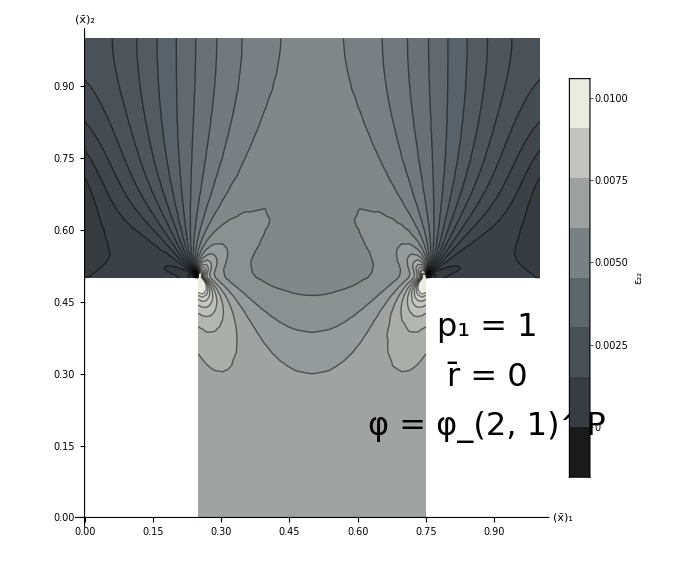

```mathematica
(*Export["TEpsR0.pdf",*)Tϵ22[ϵ22Local,"p_1 = 1", "r̄ = 0",Min[Tlocal⟦2;;All,{6}⟧],Max[Tlocal⟦2;;All,{6}⟧]]
(*Export["TEpsR005.pdf",Tϵ22[ϵ22r005p05,"p_1 = 0.5", "r̄ = 0.05",Min[Tr005p05⟦2;;All,{6}⟧],Max[Tr005p05⟦2;;All,{6}⟧]]];
Export["TEpsR01.pdf",Tϵ22[ϵ22r01p05,"p_1 = 0.5", "r̄ = 0.1",Min[Tr01p05⟦2;;All,{6}⟧],Max[Tr01p05⟦2;;All,{6}⟧]]];
Export["TEpsR015.pdf",Tϵ22[ϵ22r015p05,"p_1 = 0.5", "r̄ = 0.15",Min[Tr015p05⟦2;;All,{6}⟧],Max[Tr015p05⟦2;;All,{6}⟧]]];*)
```

```mathematica
σ22Local=Interpolation[Tlocal⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
σ22r01p075=Interpolation[Tr01p075⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
σ22r01p05=Interpolation[Tr01p05⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
σ22r01p025=Interpolation[Tr01p025⟦2;;All,{1,2,9}⟧,InterpolationOrder->1];
```

```mathematica
FS=26;
(*Export["TStressAB.pdf",*)
Show[
Plot[{σ22Local[x,0.1],σ22r01p075[x,0.1],σ22r01p05[x,0.1],σ22r01p025[x,0.1]},{x,0.25,0.75},PlotRange->Full,ImageSize->Large,
PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","(σ̄)_22"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.25],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.24],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.73],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.9],Right},CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["r̄ = 0.1",FS],Scaled[{0.35,0.4}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.65,0.4}]],
Text[Style["AB ((x̄)_2 = 0.1)",FS],Scaled[{0.5,0.95}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["TStressCD.pdf",*)
Show[
Plot[{σ22Local[x,0.45],σ22r01p075[x,0.45],σ22r01p05[x,0.45],σ22r01p025[x,0.45]},{x,0.25,0.75},PlotRange->Full,ImageSize->Large,
PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","(σ̄)_22"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.35],Below},CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.43],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.5],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.57],Below},CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["r̄ = 0.1",FS],Scaled[{0.35,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.65,0.7}]],
Text[Style["CD ((x̄)_2 = 0.45)",FS],Scaled[{0.5,0.95}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["TStressEF.pdf",*)
Show[
Plot[{σ22Local[x,0.52],σ22r01p075[x,0.52],σ22r01p05[x,0.52],σ22r01p025[x,0.52]},{x,0,1},PlotRange->Full,ImageSize->Large,
PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","(σ̄)_22"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.356],Above},FrameMargins->-4,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.39],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.63],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.57],Above},CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["r̄ = 0.1",FS],Scaled[{0.35,0.25}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.65,0.25}]],
Text[Style["EF ((x̄)_2 = 0.52)",FS],Scaled[{0.5,0.95}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["TStressGH.pdf",*)
Show[
Plot[{σ22Local[x,0.75],σ22r01p075[x,0.75],σ22r01p05[x,0.75],σ22r01p025[x,0.75]},{x,0,1},PlotRange->Full,ImageSize->Large,
PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","(σ̄)_22"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.25],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.08],Right},FrameMargins->-5,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.91],Right},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.99],Left},FrameMargins->-5,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["r̄ = 0.1",FS],Scaled[{0.35,0.4}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.65,0.4}]],
Text[Style["GH ((x̄)_2 = 0.75)",FS],Scaled[{0.5,0.75}]]
}]
]
```

-Graphics-

# Задача Кирша

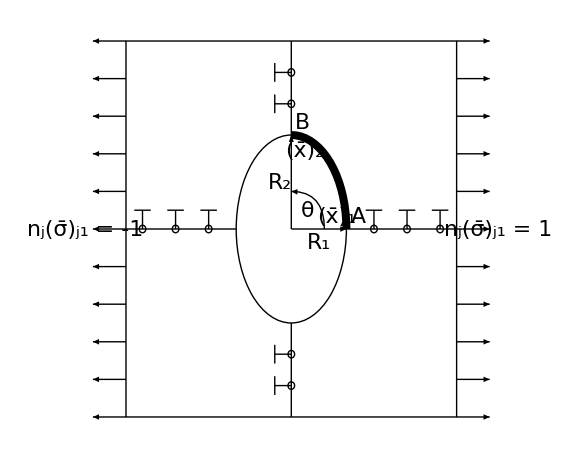

```mathematica
rect=Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}];
N0=5;
PLeft=Table[Arrow[{{-1,n/N0},{-1-2/10,n/N0}}],{n,-N0,N0}];
PRight=Table[Arrow[{{1,n/N0},{1+2/10,n/N0}}],{n,-N0,N0}];
Ellipse=Circle[{0,0},{1/3,0.5}];
rx={Arrow[{{0,0},{1/3,0}}],Text[Style["(x̄)_1",22],{1/3-0.06,0.07}],Text[Style["R_1",22],{1/6,-0.07}]};
ry={Arrow[{{0,0},{0,0.5}}],Text[Style["(x̄)_2",22],{0.08,0.42}],Text[Style["R_2",22],{-0.07,0.25}]};
σn={Rotate[Text[Style["n_j(σ̄)_j1 = -1",22],{-1.25,0}],π/2],Rotate[Text[Style["n_j(σ̄)_j1 = 1",22],{1.25,0}],π/2]};
AB={Circle[{0,0},{1/3,0.5},{0,π/2}],Text[Style["A",22],{1/3+0.07,0.07}],Text[Style["B",22],{0.07,0.57}]};
ϕArrow={Arrow[BezierCurve[{{0.2,0},{0.2,0.2},{0,0.2}}]],Text[Style["θ",22],{0.1,0.1}]};
u2Left=Table[{Line[{{-1.1+n/N0,0},{-1.1+n/N0,0.1}}],Circle[{-1.1+n/N0,0},0.02],Line[{{-1.1+n/N0-1/(4N0),0.1},{-1.1+n/N0+1/(4N0),0.1}}]},{n,1,N0-2}];
u2Right=Table[{Line[{{0.1+n/N0,0},{0.1+n/N0,0.1}}],Circle[{0.1+n/N0,0},0.02],Line[{{0.1+n/N0-1/(4N0),0.1},{0.1+n/N0+1/(4N0),0.1}}]},{n,2,N0-1}];
u1Up={Line[{{0,0.666},{-0.1,0.666}}],Line[{{0,0.833},{-0.1,0.833}}],Circle[{0,0.666},0.02],Circle[{0,0.833},0.02],Line[{{-0.1,0.616},{-0.1,0.716}}],Line[{{-0.1,0.783},{-0.1,0.883}}]};
u1Down={Line[{{0,-0.666},{-0.1,-0.666}}],Line[{{0,-0.833},{-0.1,-0.833}}],Circle[{0,-0.666},0.02],Circle[{0,-0.833},0.02],Line[{{-0.1,-0.616},{-0.1,-0.716}}],Line[{{-0.1,-0.783},{-0.1,-0.883}}]};
(*Export["EllipseStress.pdf",*)
Graphics[{Thick,Arrowheads[0.03],rect,PLeft,PRight,Ellipse,rx,ry,σn,ϕArrow,u2Left,u2Right,u1Up,u1Down,Line[{{-1,0},{-1/3,0}}],Line[{{1,0},{1/3,0}}],Line[{{0,1},{0,0.5}}],Line[{{0,-1},{0,-0.5}}],Thickness[0.01],AB},ImageSize->Large]
```

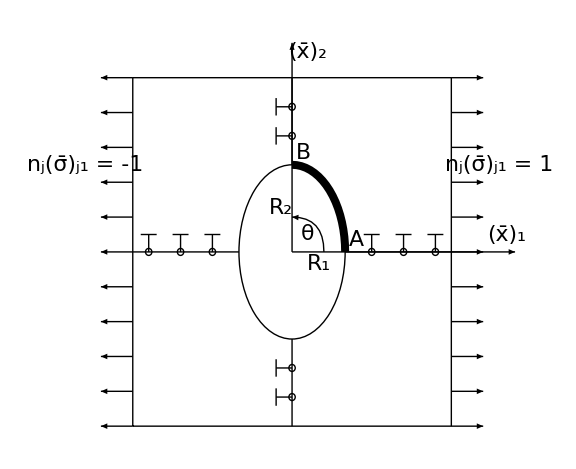

```mathematica
rect=Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}];
N0=5;
PLeft=Table[Arrow[{{-1,n/N0},{-1-2/10,n/N0}}],{n,-N0,N0}];
PRight=Table[Arrow[{{1,n/N0},{1+2/10,n/N0}}],{n,-N0,N0}];
Ellipse=Circle[{0,0},{1/3,0.5}];
rx={Arrow[{{0,0},{1.4,0}}],Text[Style["(x̄)_1",22],{1.35,0.1}],Text[Style["R_1",22],{1/6,-0.07}]};
ry={Arrow[{{0,0},{0,1.2}}],Text[Style["(x̄)_2",22],{0.1,1.15}],Text[Style["R_2",22],{-0.07,0.25}]};
σn={Rotate[Text[Style["n_j(σ̄)_j1 = -1",22],{-1.3,0.5}],π/2],Rotate[Text[Style["n_j(σ̄)_j1 = 1",22],{1.3,0.5}],π/2]};
AB={Circle[{0,0},{1/3,0.5},{0,π/2}],Text[Style["A",22],{1/3+0.07,0.07}],Text[Style["B",22],{0.07,0.57}]};
ϕArrow={Arrow[BezierCurve[{{0.2,0},{0.2,0.2},{0,0.2}}]],Text[Style["θ",22],{0.1,0.1}]};
u2Left=Table[{Line[{{-1.1+n/N0,0},{-1.1+n/N0,0.1}}],Circle[{-1.1+n/N0,0},0.02],Line[{{-1.1+n/N0-1/(4N0),0.1},{-1.1+n/N0+1/(4N0),0.1}}]},{n,1,N0-2}];
u2Right=Table[{Line[{{0.1+n/N0,0},{0.1+n/N0,0.1}}],Circle[{0.1+n/N0,0},0.02],Line[{{0.1+n/N0-1/(4N0),0.1},{0.1+n/N0+1/(4N0),0.1}}]},{n,2,N0-1}];
u1Up={Line[{{0,0.666},{-0.1,0.666}}],Line[{{0,0.833},{-0.1,0.833}}],Circle[{0,0.666},0.02],Circle[{0,0.833},0.02],Line[{{-0.1,0.616},{-0.1,0.716}}],Line[{{-0.1,0.783},{-0.1,0.883}}]};
u1Down={Line[{{0,-0.666},{-0.1,-0.666}}],Line[{{0,-0.833},{-0.1,-0.833}}],Circle[{0,-0.666},0.02],Circle[{0,-0.833},0.02],Line[{{-0.1,-0.616},{-0.1,-0.716}}],Line[{{-0.1,-0.783},{-0.1,-0.883}}]};
(*Export["EllipseStressPresentation.pdf",*)
Graphics[{Thick,Arrowheads[0.03],rect,PLeft,PRight,Ellipse,rx,ry,σn,ϕArrow,u2Left,u2Right,u1Up,u1Down,Line[{{-1,0},{-1/3,0}}],Line[{{1,0},{1/3,0}}],Line[{{0,1},{0,0.5}}],Line[{{0,-1},{0,-0.5}}],Thickness[0.01],AB},ImageSize->Large]
```

```mathematica
,
```

```mathematica
MeshData=Import["hole_mesh_example.csv"];
```

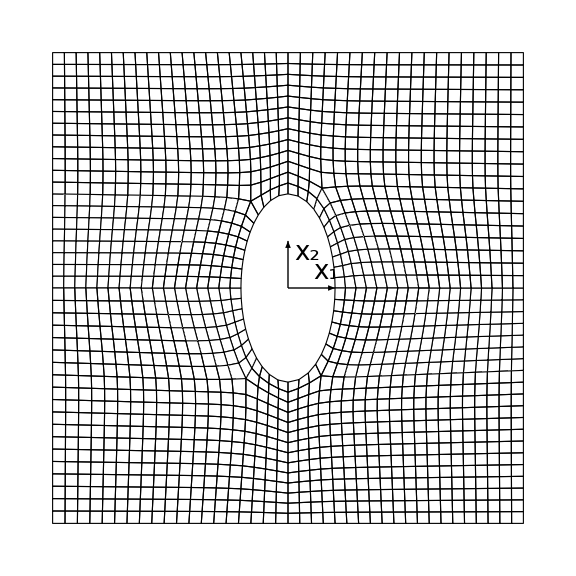

```mathematica
FS=26;
part[lst_]:=Polygon[Partition[lst,2]];
data=Map[part,MeshData];
axes={
Arrow[{{0,0},{0.2,0}}],Text[Style["x_1",FS],{0.16,0.07}],
Arrow[{{0,0},{0,0.2}}],Text[Style["x_2",FS],{0.08,0.15}]
};
(*Export["KirshMesh.pdf",*)
Graphics[{axes,EdgeForm[Directive[Black]],White,data},ImageSize->Large]
```

```mathematica
Off[NSolve::ifun];
f[ϕ_,a_,b_]:=b EllipticE[π FractionalPart[ϕ/π],1-a^2/b^2]+(b EllipticE[1-a^2/b^2]+a EllipticE[1-b^2/a^2]) IntegerPart[ϕ/π];
Kirsh050=Interpolation[Table[{ϕ,f[ϕ,0.1,0.05]/f[π/2,0.1,0.05]},{ϕ,0,π/2,π/2000}]];
Kirsh075=Interpolation[Table[{ϕ,f[ϕ,0.1,0.075]/f[π/2,0.1,0.075]},{ϕ,0,π/2,π/2000}]];
Kirsh100=Interpolation[Table[{ϕ,f[ϕ,0.1,0.1]/f[π/2,0.1,0.1]},{ϕ,0,π/2,π/2000}]];
Kirsh125=Interpolation[Table[{ϕ,f[ϕ,0.08,0.1]/f[π/2,0.08,0.1]},{ϕ,0,π/2,π/2000}]];
Kirsh150=Interpolation[Table[{ϕ,f[ϕ,1/15,0.1]/f[π/2,1/15,0.1]},{ϕ,0,π/2,π/2000}]];
Φ050=Interpolation[Table[{z,(x/.NSolve[Kirsh050[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ075=Interpolation[Table[{z,(x/.NSolve[Kirsh075[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ100=Interpolation[Table[{z,(x/.NSolve[Kirsh100[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ125=Interpolation[Table[{z,(x/.NSolve[Kirsh125[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ150=Interpolation[Table[{z,(x/.NSolve[Kirsh150[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
```

```mathematica
Kirsh050Local=Import["data/Kirsh/Kirsh050/local/solution_mechanical_2d.csv"];
Kirsh075Local=Import["data/Kirsh/Kirsh075/local/solution_mechanical_2d.csv"];
Kirsh100Local=Import["data/Kirsh/Kirsh100/local/solution_mechanical_2d.csv"];
Kirsh125Local=Import["data/Kirsh/Kirsh125/local/solution_mechanical_2d.csv"];
Kirsh150Local=Import["data/Kirsh/Kirsh150/local/solution_mechanical_2d.csv"];
```

```mathematica
ϵ11[data_,Φ_,R1_,R2_]:={
tmp=Interpolation[data⟦2;;All,{1,2,5}⟧,InterpolationOrder->1];
tmp =Table[{x,tmp[R1 Cos[Φ[x]],R2 Sin[Φ[x]]]},{x,0,1,0.001}];
Interpolation[Table[{x,ResourceFunction["Loess"][tmp,100,x]},{x,0,1,0.001}]]
}
```

```mathematica
ϵ11050Local=ϵ11[Kirsh050Local,Φ050,0.1,0.05]⟦1⟧;
ϵ11075Local=ϵ11[Kirsh075Local,Φ075,0.1,0.075]⟦1⟧;
ϵ11100Local=ϵ11[Kirsh100Local,Φ100,0.1,0.1]⟦1⟧;
ϵ11125Local=ϵ11[Kirsh125Local,Φ125,0.08,0.1]⟦1⟧;
ϵ11150Local=ϵ11[Kirsh150Local,Φ150,1/15,0.1]⟦1⟧;
```

```mathematica
FS=26;
(*Export["KirshABEps11Local.pdf",*)
Show[
Plot[{ϵ11050Local[x],ϵ11075Local[x],ϵ11100Local[x],ϵ11125Local[x],ϵ11150Local[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","ε_11"},
PlotLabels->{
Callout["ρ = 0.5",{Scaled[0.45],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["ρ = 0.75",{Scaled[0.73],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1",{Scaled[0.58],Right},CalloutMarker->"Arrow"],
Callout["ρ = 1.25",{Scaled[0.73],Right},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1.5",{Scaled[0.95],Left},FrameMargins->0,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p_1 = 1",FS],Scaled[{0.2,0.85}]],
Text[Style["r̄ = 0",FS],Scaled[{0.2,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.2,0.55}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["KirshABEps11LocalPresentation.pdf",*)
Show[
Plot[{ϵ11050Local[x],ϵ11075Local[x],ϵ11100Local[x],ϵ11125Local[x],ϵ11150Local[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Rainbow",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","ε_11"},
PlotLabels->{
Callout["ρ = 0.5",{Scaled[0.45],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["ρ = 0.75",{Scaled[0.73],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1",{Scaled[0.58],Right},CalloutMarker->"Arrow"],
Callout["ρ = 1.25",{Scaled[0.73],Right},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1.5",{Scaled[0.95],Left},FrameMargins->0,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p_1 = 1",FS],Scaled[{0.2,0.85}]],
Text[Style["r̄ = 0",FS],Scaled[{0.2,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.2,0.55}]]
}]
]
```

-Graphics-

```mathematica
Kirsh050r005p05=Import["data/Kirsh/Kirsh050/r005p05/solution_mechanical_2d.csv"];
Kirsh075r005p05=Import["data/Kirsh/Kirsh075/r005p05/solution_mechanical_2d.csv"];
Kirsh100r005p05=Import["data/Kirsh/Kirsh100/r005p05/solution_mechanical_2d.csv"];
Kirsh125r005p05=Import["data/Kirsh/Kirsh125/r005p05/solution_mechanical_2d.csv"];
Kirsh150r005p05=Import["data/Kirsh/Kirsh150/r005p05/solution_mechanical_2d.csv"];
```

```mathematica
ϵ11050r005p05=ϵ11[Kirsh050r005p05,Φ050,0.1,0.05]⟦1⟧;
ϵ11075r005p05=ϵ11[Kirsh075r005p05,Φ075,0.1,0.075]⟦1⟧;
ϵ11100r005p05=ϵ11[Kirsh100r005p05,Φ100,0.1,0.1]⟦1⟧;
ϵ11125r005p05=ϵ11[Kirsh125r005p05,Φ125,0.08,0.1]⟦1⟧;
ϵ11150r005p05=ϵ11[Kirsh150r005p05,Φ150,1/15,0.1]⟦1⟧;
```

```mathematica
FS=26;
(*Export["KirshABEps11r005p05.pdf",*)
Show[
Plot[{ϵ11050r005p05[x],ϵ11075r005p05[x],ϵ11100r005p05[x],ϵ11125r005p05[x],ϵ11150r005p05[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","ε_11"},
PlotLabels->{
Callout["ρ = 0.5",{Scaled[0.45],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["ρ = 0.75",{Scaled[0.74],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1",{Scaled[0.65],Right},CalloutMarker->"Arrow"],
Callout["ρ = 1.25",{Scaled[0.73],Right},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1.5",{Scaled[0.95],Left},FrameMargins->0,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.85}]],
Text[Style["r̄ = 0.05",FS],Scaled[{0.2,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.2,0.55}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["KirshABEps11r005p05Presentation.pdf",*)
Show[
Plot[{ϵ11050r005p05[x],ϵ11075r005p05[x],ϵ11100r005p05[x],ϵ11125r005p05[x],ϵ11150r005p05[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Rainbow",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","ε_11"},
PlotLabels->{
Callout["ρ = 0.5",{Scaled[0.45],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["ρ = 0.75",{Scaled[0.74],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1",{Scaled[0.65],Right},CalloutMarker->"Arrow"],
Callout["ρ = 1.25",{Scaled[0.73],Right},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1.5",{Scaled[0.95],Left},FrameMargins->0,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.85}]],
Text[Style["r̄ = 0.05",FS],Scaled[{0.2,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.2,0.55}]]
}]
]
```

-Graphics-

```mathematica
CircleLocal=Import["data/Kirsh/Kirsh100/local/solution_mechanical_2d.csv"];
Circler0025p05=Import["data/Kirsh/Kirsh100/r0025p05/solution_mechanical_2d.csv"];
Circler005p075=Import["data/Kirsh/Kirsh100/r005p075/solution_mechanical_2d.csv"];
Circler005p05=Import["data/Kirsh/Kirsh100/r005p05/solution_mechanical_2d.csv"];
Circler005p025=Import["data/Kirsh/Kirsh100/r005p025/solution_mechanical_2d.csv"];
Circler01p05=Import["data/Kirsh/Kirsh100/r01p05/solution_mechanical_2d.csv"];
```

```mathematica
Circleϵ11050Local=ϵ11[CircleLocal,Φ100,0.1,0.1]⟦1⟧;
Circleϵ11075r0025p05=ϵ11[Circler0025p05,Φ100,0.1,0.1]⟦1⟧;
Circleϵ11100r005p075=ϵ11[Circler005p075,Φ100,0.1,0.1]⟦1⟧;
Circleϵ11125r005p05=ϵ11[Circler005p05,Φ100,0.1,0.1]⟦1⟧;
Circleϵ11150r005p025=ϵ11[Circler005p025,Φ100,0.1,0.1]⟦1⟧;
Circleϵ11150r01p05=ϵ11[Circler01p05,Φ100,0.1,0.1]⟦1⟧;
```

```mathematica
FS=26;
(*Export["KirshABEps11VariationP1.pdf",*)
Show[
Plot[{Circleϵ11050Local[x],Circleϵ11100r005p075[x],Circleϵ11125r005p05[x],Circleϵ11150r005p025[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","ε_11"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.85],Right},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.5],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.58],Right},CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.68],Right},FrameMargins->1,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["ρ = 1",FS],Scaled[{0.2,0.85}]],
Text[Style["r̄ = 0.05",FS],Scaled[{0.2,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.2,0.55}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["KirshABEps11VariationR.pdf",*)
Show[
Plot[{Circleϵ11050Local[x],Circleϵ11075r0025p05[x],Circleϵ11125r005p05[x],Circleϵ11150r01p05[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","ε_11"},
PlotLabels->{
Callout["r̄ = 0",{Scaled[0.85],Right},Background->Transparent,CalloutMarker->"Arrow"],
Callout["r̄ = 0.025",{Scaled[0.4],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["r̄ = 0.05",{Scaled[0.57],Right},CalloutMarker->"Arrow"],
Callout["r̄ = 0.1",{Scaled[0.8],Left},FrameMargins->1,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["ρ = 1",FS],Scaled[{0.2,0.85}]],
Text[Style["p_1 = 0.5",FS],Scaled[{0.2,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.2,0.55}]]
}]
]
```

-Graphics-

```mathematica
FS=32;
Circleϵ11[ϵ11_,p1_,r_,min_,max_]:=Show[
ContourPlot[ϵ11[x,y],{x,0,1},{y,0,1},RegionFunction->Function[{x,y,z},x^2+y^2>=0.1^2],PlotRange->{0,0.005},ClippingStyle->{Black,ColorData["GrayTones"][0.9999]},
ImageSize->Large,PlotRange->Full,ColorFunction->"GrayTones",ColorFunctionScaling->True,Frame->False,Axes->True,(*PlotLegends->Placed[BarLegend[{-0.001,0,0.002,0.003,0.004},LegendLabel->"ε_22"],After],*)
PlotLegends->BarLegend[{Automatic,{min,max}},8,LegendLabel->"ε_11",LabelingFunction->(Round[#,0.0001]&)],
LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"(x̄)_1","(x̄)_2"},Contours->32,ContourStyle->Black],
Graphics[{
Text[Style[p1,FS],Scaled[{0.75,0.5}]],
Text[Style[r,FS],Scaled[{0.75,0.4}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.75,0.3}]],
Text[Style["R_1 = R_2 = 0.1",FS],Scaled[{0.75,0.2}]]
}]
]
```

```mathematica
Export["CircleEps11Local.pdf",Circleϵ11[CircleEps11Local,"p_1 = 1","r̄ = 0",Min[CircleLocal⟦2;;All,{5}⟧],Max[CircleLocal⟦2;;All,{5}⟧]]];
Export["CircleEps11r0025p05.pdf",Circleϵ11[CircleEps11r0025p05,"p_1 = 0.5","r̄ = 0.025",Min[Circler0025p05⟦2;;All,{5}⟧],Max[Circler0025p05⟦2;;All,{5}⟧]]];
Export["CircleEps11r005p05.pdf",Circleϵ11[CircleEps11r005p05,"p_1 = 0.5","r̄ = 0.05",Min[Circler005p05⟦2;;All,{5}⟧],Max[Circler005p05⟦2;;All,{5}⟧]]];
Export["CircleEps11r01p05.pdf",Circleϵ11[CircleEps11r01p05,"p_1 = 0.5","r̄ = 0.1",Min[Circler01p05⟦2;;All,{5}⟧],Max[Circler01p05⟦2;;All,{5}⟧]]];
```

# Тепловая задача Кирша

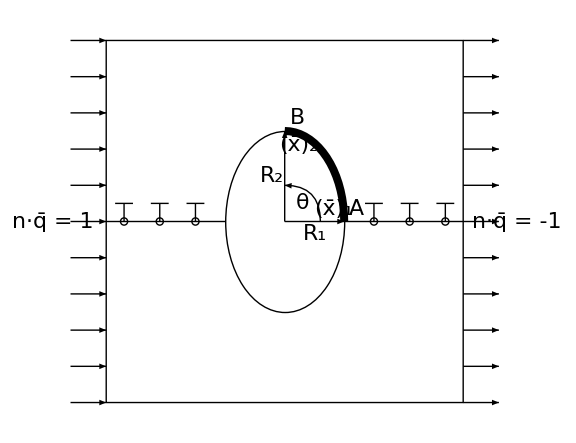

```mathematica
N0=5;
M0=10;
FS=22;
points={{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}};
Ellipse=Circle[{0,0},{1/3,0.5}];
symmetryLeft={{-1,0},{-1/3,0}};
symmetryRight={{1,0},{1/3,0}};
rx={Arrow[{{0,0},{1/3,0}}],Text[Style["(x̄)_1",22],{1/3-0.06,0.07}],Text[Style["R_1",22],{1/6,-0.07}]};
ry={Arrow[{{0,0},{0,0.5}}],Text[Style["(x̄)_2",22],{0.08,0.42}],Text[Style["R_2",22],{-0.07,0.25}]};
θArrow={Arrow[BezierCurve[{{0.2,0},{0.2,0.2},{0,0.2}}]],Text[Style["θ",22],{0.1,0.1}]};
u2Left=Table[{Line[{{-1.1+n/N0,0},{-1.1+n/N0,0.1}}],Circle[{-1.1+n/N0,0},0.02],Line[{{-1.1+n/N0-1/(4N0),0.1},{-1.1+n/N0+1/(4N0),0.1}}]},{n,1,N0-2}];
u2Right=Table[{Line[{{0.1+n/N0,0},{0.1+n/N0,0.1}}],Circle[{0.1+n/N0,0},0.02],Line[{{0.1+n/N0-1/(4N0),0.1},{0.1+n/N0+1/(4N0),0.1}}]},{n,2,N0-1}];
ql=Table[Arrow[{{-1.2,(2n)/M0-1},{-1,(2n)/M0-1}}],{n,0,M0}];
qr=Table[Arrow[{{1,(2n)/M0-1},{1.2,(2n)/M0-1}}],{n,0,M0}];
flux={Rotate[Text[Style["n·q̄ = 1",FS],{-1.3,0}],π/2],Rotate[Text[Style["n·q̄ = -1",22],{1.3,0}],π/2]};
CD={Circle[{0,0},{1/3,0.5},{0,π/2}],Text[Style["C",22],{1/3+0.1,0}],Text[Style["D",22],{0,0.6}]};
AB={Circle[{0,0},{1/3,0.5},{0,π/2}],Text[Style["A",22],{1/3+0.07,0.07}],Text[Style["B",22],{0.07,0.57}]};
(*Export["EllipseThermal.pdf",*)
Graphics[{Thick,Arrowheads[0.03],Line[points],Ellipse,Line[symmetryLeft],Line[symmetryRight],rx,ry,θArrow,u2Left,u2Right,ql,qr,flux,Thickness[0.01],AB},ImageSize->Large]
```

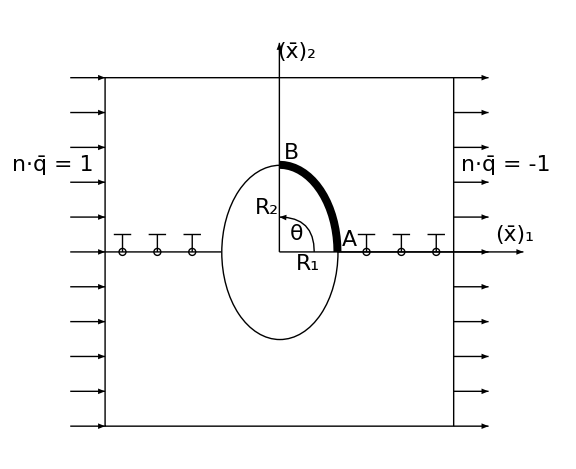

```mathematica
N0=5;
M0=10;
FS=22;
points={{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}};
Ellipse=Circle[{0,0},{1/3,0.5}];
symmetryLeft={{-1,0},{-1/3,0}};
symmetryRight={{1,0},{1/3,0}};
rx={Arrow[{{0,0},{1.4,0}}],Text[Style["(x̄)_1",22],{1.35,0.1}],Text[Style["R_1",22],{1/6,-0.07}]};
ry={Arrow[{{0,0},{0,1.2}}],Text[Style["(x̄)_2",22],{0.1,1.15}],Text[Style["R_2",22],{-0.07,0.25}]};
θArrow={Arrow[BezierCurve[{{0.2,0},{0.2,0.2},{0,0.2}}]],Text[Style["θ",22],{0.1,0.1}]};
u2Left=Table[{Line[{{-1.1+n/N0,0},{-1.1+n/N0,0.1}}],Circle[{-1.1+n/N0,0},0.02],Line[{{-1.1+n/N0-1/(4N0),0.1},{-1.1+n/N0+1/(4N0),0.1}}]},{n,1,N0-2}];
u2Right=Table[{Line[{{0.1+n/N0,0},{0.1+n/N0,0.1}}],Circle[{0.1+n/N0,0},0.02],Line[{{0.1+n/N0-1/(4N0),0.1},{0.1+n/N0+1/(4N0),0.1}}]},{n,2,N0-1}];
ql=Table[Arrow[{{-1.2,(2n)/M0-1},{-1,(2n)/M0-1}}],{n,0,M0}];
qr=Table[Arrow[{{1,(2n)/M0-1},{1.2,(2n)/M0-1}}],{n,0,M0}];
flux={Rotate[Text[Style["n·q̄ = 1",FS],{-1.3,0.5}],π/2],Rotate[Text[Style["n·q̄ = -1",22],{1.3,0.5}],π/2]};
CD={Circle[{0,0},{1/3,0.5},{0,π/2}],Text[Style["C",22],{1/3+0.1,0}],Text[Style["D",22],{0,0.6}]};
AB={Circle[{0,0},{1/3,0.5},{0,π/2}],Text[Style["A",22],{1/3+0.07,0.07}],Text[Style["B",22],{0.07,0.57}]};
(*Export["EllipseThermalPresentation.pdf",*)
Graphics[{Thick,Arrowheads[0.03],Line[points],Ellipse,Line[symmetryLeft],Line[symmetryRight],rx,ry,θArrow,u2Left,u2Right,ql,qr,flux,Thickness[0.01],AB},ImageSize->Large]
```

```mathematica
Off[NSolve::ifun];
f[ϕ_,a_,b_]:=b EllipticE[π FractionalPart[ϕ/π],1-a^2/b^2]+(b EllipticE[1-a^2/b^2]+a EllipticE[1-b^2/a^2]) IntegerPart[ϕ/π];
Kirsh050=Interpolation[Table[{ϕ,f[ϕ,0.1,0.05]/f[π/2,0.1,0.05]},{ϕ,0,π/2,π/2000}]];
Kirsh075=Interpolation[Table[{ϕ,f[ϕ,0.1,0.075]/f[π/2,0.1,0.075]},{ϕ,0,π/2,π/2000}]];
Kirsh100=Interpolation[Table[{ϕ,f[ϕ,0.1,0.1]/f[π/2,0.1,0.1]},{ϕ,0,π/2,π/2000}]];
Kirsh125=Interpolation[Table[{ϕ,f[ϕ,0.08,0.1]/f[π/2,0.08,0.1]},{ϕ,0,π/2,π/2000}]];
Kirsh150=Interpolation[Table[{ϕ,f[ϕ,1/15,0.1]/f[π/2,1/15,0.1]},{ϕ,0,π/2,π/2000}]];
Φ050=Interpolation[Table[{z,(x/.NSolve[Kirsh050[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ075=Interpolation[Table[{z,(x/.NSolve[Kirsh075[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ100=Interpolation[Table[{z,(x/.NSolve[Kirsh100[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ125=Interpolation[Table[{z,(x/.NSolve[Kirsh125[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
Φ150=Interpolation[Table[{z,(x/.NSolve[Kirsh150[x]==z,x])⟦1⟧},{z,0,1,0.001}]];
```

```mathematica
ThermalKirsh050Local=Import["data/ThermalKirsh/Kirsh050/Local/solution_2d.csv"];
ThermalKirsh075Local=Import["data/ThermalKirsh/Kirsh075/Local/solution_2d.csv"];
ThermalKirsh100Local=Import["data/ThermalKirsh/Kirsh100/Local/solution_2d.csv"];
ThermalKirsh125Local=Import["data/ThermalKirsh/Kirsh125/Local/solution_2d.csv"];
ThermalKirsh150Local=Import["data/ThermalKirsh/Kirsh150/Local/solution_2d.csv"];
```

```mathematica
interpolate[data_,Φ_,R1_,R2_,number_]:={
tmp=Interpolation[data⟦2;;All,{1,2,number}⟧,InterpolationOrder->1];
tmp =Table[{x,tmp[R1 Cos[Φ[x]],R2 Sin[Φ[x]]]},{x,0,1,0.01}];
(*Interpolation[tmp,InterpolationOrder->1]*)
Interpolation[Table[{x,ResourceFunction["Loess"][tmp,20,x]},{x,0,1,0.001}]]
}⟦1⟧;
```

```mathematica
σ11050Local=interpolate[ThermalKirsh050Local,Φ050,0.1,0.05,11];
σ11075Local=interpolate[ThermalKirsh075Local,Φ075,0.1,0.075,11];
σ11100Local=interpolate[ThermalKirsh100Local,Φ100,0.1,0.1,11];
σ11125Local=interpolate[ThermalKirsh125Local,Φ125,0.08,0.1,11];
σ11150Local=interpolate[ThermalKirsh150Local,Φ150,1/15,0.1,11];
```

```mathematica
FS=26;
(*Export["ThermalKirshSigma11Local.pdf",*)
Show[
Plot[{σ11050Local[x],σ11075Local[x],σ11100Local[x],σ11125Local[x],σ11150Local[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","(σ̄)_11"},
PlotLabels->{
Callout["ρ = 0.5",{Scaled[0.7],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["ρ = 0.75",{Scaled[0.75],Below},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1",{Scaled[0.8],Below},CalloutMarker->"Arrow"],
Callout["ρ = 1.25",{Scaled[0.55],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1.5",{Scaled[0.75],Above},FrameMargins->0,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p_1 = 1",FS],Scaled[{0.15,0.9}]],
Text[Style["r̄ = 0",FS],Scaled[{0.15,0.75}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["ThermalKirshSigma11LocalPresentation.pdf",*)
Show[
Plot[{σ11050Local[x],σ11075Local[x],σ11100Local[x],σ11125Local[x],σ11150Local[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Rainbow",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","(σ̄)_11"},
PlotLabels->{
Callout["ρ = 0.5",{Scaled[0.7],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["ρ = 0.75",{Scaled[0.75],Below},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1",{Scaled[0.8],Below},CalloutMarker->"Arrow"],
Callout["ρ = 1.25",{Scaled[0.55],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1.5",{Scaled[0.75],Above},FrameMargins->0,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p_1 = 1",FS],Scaled[{0.15,0.9}]],
Text[Style["r̄ = 0",FS],Scaled[{0.15,0.75}]]
}]
]
```

-Graphics-

```mathematica
σ22050Local=interpolate[ThermalKirsh050Local,Φ050,0.1,0.05,12];
σ22075Local=interpolate[ThermalKirsh075Local,Φ075,0.1,0.075,12];
σ22100Local=interpolate[ThermalKirsh100Local,Φ100,0.1,0.1,12];
σ22125Local=interpolate[ThermalKirsh125Local,Φ125,0.08,0.1,12];
σ22150Local=interpolate[ThermalKirsh150Local,Φ150,1/15,0.1,12];
```

```mathematica
FS=26;
(*Export["ThermalKirshSigma22Local.pdf",*)
Show[
Plot[{σ22050Local[x],σ22075Local[x],σ22100Local[x],σ22125Local[x],σ22150Local[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","(σ̄)_22"},
PlotLabels->{
Callout["ρ = 0.5",{Scaled[0.24],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["ρ = 0.75",{Scaled[0.3],Below},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1",{Scaled[0.5],Below},CalloutMarker->"Arrow"],
Callout["ρ = 1.25",{Scaled[0.7],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1.5",{Scaled[0.7],Above},FrameMargins->0,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p_1 = 1",FS],Scaled[{0.9,0.9}]],
Text[Style["r̄ = 0",FS],Scaled[{0.9,0.75}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["ThermalKirshSigma22LocalPresentation.pdf",*)
Show[
Plot[{σ22050Local[x],σ22075Local[x],σ22100Local[x],σ22125Local[x],σ22150Local[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Rainbow",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","(σ̄)_22"},
PlotLabels->{
Callout["ρ = 0.5",{Scaled[0.24],Below},Background->Transparent,CalloutMarker->"Arrow"],
Callout["ρ = 0.75",{Scaled[0.3],Below},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1",{Scaled[0.5],Below},CalloutMarker->"Arrow"],
Callout["ρ = 1.25",{Scaled[0.7],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["ρ = 1.5",{Scaled[0.7],Above},FrameMargins->0,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["p_1 = 1",FS],Scaled[{0.9,0.9}]],
Text[Style["r̄ = 0",FS],Scaled[{0.9,0.75}]]
}]
]
```

-Graphics-

```mathematica
ThermalKirsh100Local=Import["data/ThermalKirsh/Kirsh100/Local/solution_2d.csv"];
ThermalKirsh100p075r005=Import["data/ThermalKirsh/Kirsh100/r005_p075/solution_2d.csv"];
ThermalKirsh100p05r005=Import["data/ThermalKirsh/Kirsh100/r005_p05/solution_2d.csv"];
ThermalKirsh100p025r005=Import["data/ThermalKirsh/Kirsh100/r005_p025/solution_2d.csv"];
```

```mathematica
σ11050Local=interpolate[ThermalKirsh100Local,Φ100,0.1,0.1,11];
σ11075p075r005=interpolate[ThermalKirsh100p075r005,Φ100,0.1,0.1,11];
σ11100p05r005=interpolate[ThermalKirsh100p05r005,Φ100,0.1,0.1,11];
σ11125p025r005=interpolate[ThermalKirsh100p025r005,Φ100,0.1,0.1,11];
```

```mathematica
FS=26;
(*Export["ThermalKirshSigma11VariationP1.pdf",*)
Show[
Plot[{σ11050Local[x],σ11075p075r005[x],σ11100p05r005[x],σ11125p025r005[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","(σ̄)_11"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.7],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.6],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.4],Below},CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.3],Below},FrameMargins->1,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["ρ = 1",FS],Scaled[{0.2,0.85}]],
Text[Style["r̄ = 0.05",FS],Scaled[{0.2,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.2,0.55}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["ThermalKirshSigma11VariationP1Presentation.pdf",*)
Show[
Plot[{σ11050Local[x],σ11075p075r005[x],σ11100p05r005[x],σ11125p025r005[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Rainbow",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","(σ̄)_11"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.7],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.6],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.4],Below},CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.3],Below},FrameMargins->1,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["ρ = 1",FS],Scaled[{0.2,0.85}]],
Text[Style["r̄ = 0.05",FS],Scaled[{0.2,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.2,0.55}]]
}]
]
```

-Graphics-

```mathematica
σ22050Local=interpolate[ThermalKirsh100Local,Φ100,0.1,0.1,12];
σ22075p075r005=interpolate[ThermalKirsh100p075r005,Φ100,0.1,0.1,12];
σ22100p05r005=interpolate[ThermalKirsh100p05r005,Φ100,0.1,0.1,12];
σ22125p025r005=interpolate[ThermalKirsh100p025r005,Φ100,0.1,0.1,12];
```

```mathematica
FS=26;
(*Export["ThermalKirshSigma22VariationP1.pdf",*)
Show[
Plot[{σ22050Local[x],σ22075p075r005[x],σ22100p05r005[x],σ22125p025r005[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","(σ̄)_22"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.3],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.4],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.5],Below},CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.35],Below},FrameMargins->1,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["ρ = 1",FS],Scaled[{0.9,0.85}]],
Text[Style["r̄ = 0.05",FS],Scaled[{0.9,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.9,0.55}]]
}]
]
```

-Graphics-

```mathematica
FS=26;
(*Export["ThermalKirshSigma22VariationP1Presentation.pdf",*)
Show[
Plot[{σ22050Local[x],σ22075p075r005[x],σ22100p05r005[x],σ22125p025r005[x]},{x,0,1},
PlotRange->Full,ImageSize->Large,PlotTheme->"Rainbow",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"l̄","(σ̄)_22"},
PlotLabels->{
Callout["p_1 = 1",{Scaled[0.3],Above},Background->Transparent,CalloutMarker->"Arrow"],
Callout["p_1 = 0.75",{Scaled[0.4],Above},FrameMargins->1,CalloutMarker->"Arrow"],
Callout["p_1 = 0.5",{Scaled[0.5],Below},CalloutMarker->"Arrow"],
Callout["p_1 = 0.25",{Scaled[0.35],Below},FrameMargins->1,CalloutMarker->"Arrow"]
}],
Graphics[{
Text[Style["ρ = 1",FS],Scaled[{0.9,0.85}]],
Text[Style["r̄ = 0.05",FS],Scaled[{0.9,0.7}]],
Text[Style["φ = φ_(2, 1)^P",FS],Scaled[{0.9,0.55}]]
}]
]
```

-Graphics-

# Исследование сходимости

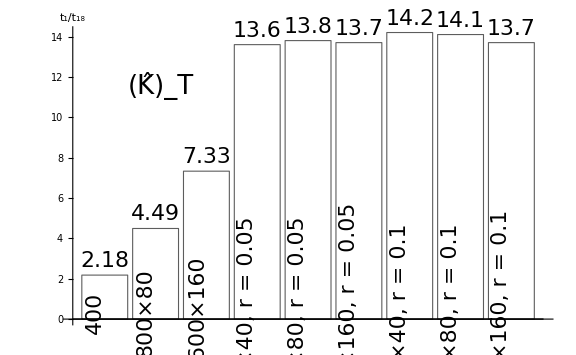

```mathematica
(*Export["OMPThermal.pdf",*)
Show[
BarChart[{{
Labeled[Round[0.061/0.028,0.01],Rotate["400",90 Degree],Bottom],
Labeled[Round[0.521/0.116,0.01],Rotate["800×80",90 Degree],Bottom],
Labeled[Round[5.17/0.705,0.01],Rotate["1600×160",π/2],Bottom],
Labeled[Round[14.4/1.055,0.1],Rotate["400×40, r = 0.05",π/2],Bottom],
Labeled[Round[157/11.37,0.1],Rotate["800×80, r = 0.05",π/2],Bottom],
Labeled[Round[1825/132.9,0.1],Rotate["1600×160, r = 0.05",π/2],Bottom],
Labeled[Round[38/2.68,0.1],Rotate["400×40, r = 0.1",π/2],Bottom],
Labeled[Round[450/32,0.1],Rotate["800×80, r = 0.1",π/2],Bottom],
Labeled[Round[6134/447,0.1],Rotate["1600×160, r = 0.1",π/2],Bottom]
}},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"","t_1/t_18"},LabelingFunction->Above,ChartStyle->Directive[EdgeForm[{Thick,Black}], White]],
Graphics[
Text[Style["(K̂)_T",FS],Scaled[{0.2,0.8}]]
]
]
```

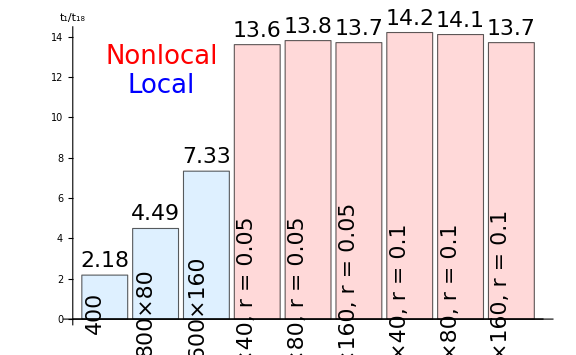

```mathematica
(*Export["OMPThermalPresentation.pdf",*)
Show[
BarChart[{{
Style[Labeled[Round[0.061/0.028,0.01],Rotate["400",90 Degree],Bottom],LightBlue],
Style[Labeled[Round[0.521/0.116,0.01],Rotate["800×80",90 Degree],Bottom],LightBlue],
Style[Labeled[Round[5.17/0.705,0.01],Rotate["1600×160",π/2],Bottom],LightBlue],
Style[Labeled[Round[14.4/1.055,0.1],Rotate["400×40, r = 0.05",π/2],Bottom],LightRed],
Style[Labeled[Round[157/11.37,0.1],Rotate["800×80, r = 0.05",π/2],Bottom],LightRed],
Style[Labeled[Round[1825/132.9,0.1],Rotate["1600×160, r = 0.05",π/2],Bottom],LightRed],
Style[Labeled[Round[38/2.68,0.1],Rotate["400×40, r = 0.1",π/2],Bottom],LightRed],
Style[Labeled[Round[450/32,0.1],Rotate["800×80, r = 0.1",π/2],Bottom],LightRed],
Style[Labeled[Round[6134/447,0.1],Rotate["1600×160, r = 0.1",π/2],Bottom],LightRed]
}},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"","t_1/t_18"},LabelingFunction->Above,ChartStyle->Directive[EdgeForm[{Thick,Black}], White]],
Graphics[
Graphics[{
Text[Style["Nonlocal",FS,Red],Scaled[{0.2,0.9}]],
Text[Style["Local",FS,Blue],Scaled[{0.2,0.8}]]
}]
]
]
```

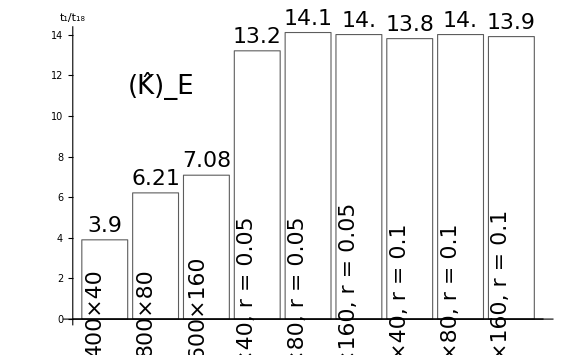

```mathematica
(*Export["OMPMechanical.pdf",*)
Show[
BarChart[{{
Labeled[Round[0.187/0.048,0.01],Rotate["400×40",90 Degree],Bottom],
Labeled[Round[1.701/0.274,0.01],Rotate["800×80",90 Degree],Bottom],
Labeled[Round[16.76/2.366,0.01],Rotate["1600×160",π/2],Bottom],
Labeled[Round[17.06/1.288,0.1],Rotate["400×40, r = 0.05",π/2],Bottom],
Labeled[Round[187/13.3,0.1],Rotate["800×80, r = 0.05",π/2],Bottom],
Labeled[Round[2166/155,0.1],Rotate["1600×160, r = 0.05",π/2],Bottom],
Labeled[Round[44.9/3.26,0.1],Rotate["400×40, r = 0.1",π/2],Bottom],
Labeled[Round[529/37.8,0.1],Rotate["800×80, r = 0.1",π/2],Bottom],
Labeled[Round[7266/521,0.1],Rotate["1600×160, r = 0.1",π/2],Bottom]
}},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"","t_1/t_18"},LabelingFunction->Above,ChartStyle->Directive[EdgeForm[{Thick,Black}], White]],
Graphics[
Text[Style["(K̂)_E",FS],Scaled[{0.2,0.8}]]
]
]
```

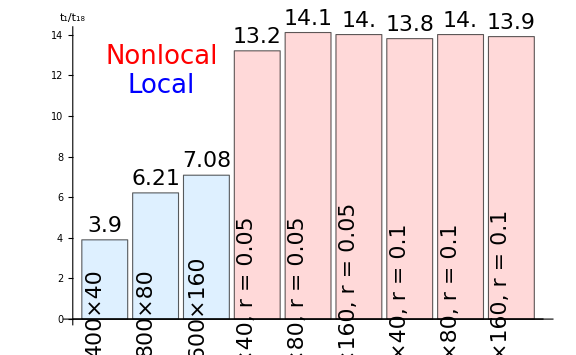

```mathematica
(*Export["OMPMechanicalPresentation.pdf",*)
Show[
BarChart[{{
Style[Labeled[Round[0.187/0.048,0.01],Rotate["400×40",90 Degree],Bottom],LightBlue],
Style[Labeled[Round[1.701/0.274,0.01],Rotate["800×80",90 Degree],Bottom],LightBlue],
Style[Labeled[Round[16.76/2.366,0.01],Rotate["1600×160",π/2],Bottom],LightBlue],
Style[Labeled[Round[17.06/1.288,0.1],Rotate["400×40, r = 0.05",π/2],Bottom],LightRed],
Style[Labeled[Round[187/13.3,0.1],Rotate["800×80, r = 0.05",π/2],Bottom],LightRed],
Style[Labeled[Round[2166/155,0.1],Rotate["1600×160, r = 0.05",π/2],Bottom],LightRed],
Style[Labeled[Round[44.9/3.26,0.1],Rotate["400×40, r = 0.1",π/2],Bottom],LightRed],
Style[Labeled[Round[529/37.8,0.1],Rotate["800×80, r = 0.1",π/2],Bottom],LightRed],
Style[Labeled[Round[7266/521,0.1],Rotate["1600×160, r = 0.1",π/2],Bottom],LightRed]
}},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"","t_1/t_18"},LabelingFunction->Above,ChartStyle->Directive[EdgeForm[{Thick,Black}], White]],
Graphics[{
Text[Style["Nonlocal",FS,Red],Scaled[{0.2,0.9}]],
Text[Style["Local",FS,Blue],Scaled[{0.2,0.8}]]
}]
]
```

```mathematica
1541119523*16./1024/1024/1024
```

22.9645

```mathematica
(*Export["PieChartNoBalance.pdf",*)
PieChart[{63.0,60.7,26.4,25.1,23.1,23},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"63.1 Gb","60.7 Gb","26.4 Gb","25.1 Gb","23.1 Gb","23 Gb"}]
```

-Graphics-

```mathematica
(*Export["PieChartBalance.pdf",*)
PieChart[{36.9,36.9,36.9,36.9,36.9,36.9},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"36.9 Gb","36.9 Gb","36.9 Gb","36.9 Gb","36.9 Gb","36.9 Gb"}]
```

-Graphics-

```mathematica
FS=26;
s={-3/9,-2/9,-1/9,0,1/9,2/9,3/9,4/9,5/9,6/9,7/9};
```

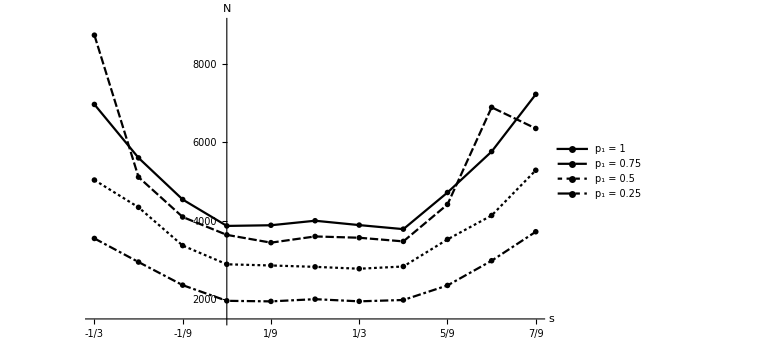

```mathematica
ThermalLocalIt=Transpose[{s,{6961,5600,4540,3868,3885,4000,3889,3786,4719,5761,7218}}];
Thermalr01p075It=Transpose[{s,{8724,5110,4095,3640,3442,3600,3567,3474,4415,6887,6349}}];
Thermalr01p05It=Transpose[{s,{5036,4341,3367,2891,2861,2826,2778,2835,3525,4134,5285}}];
Thermalr01p025It=Transpose[{s,{3549,2948,2360,1961,1947,2003,1948,1982,2353,2982,3720}}];
(*Export["ThermalIter.pdf",*)
ListLinePlot[{ThermalLocalIt,Thermalr01p075It,Thermalr01p05It,Thermalr01p025It},ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"s","N"},Ticks->{s,{2000,4000,6000,8000}},PlotRange->{1500,9000},
PlotLegends->Placed[{"p_1 = 1","p_1 = 0.75","p_1 = 0.5","p_1 = 0.25"},Scaled[{0.5,0.75}]]]
```

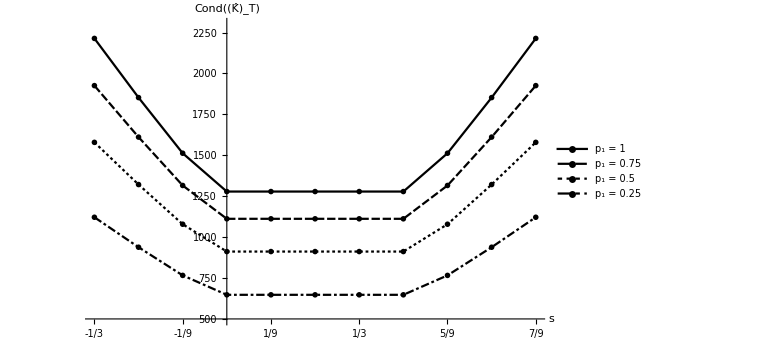

```mathematica
ThermalLocalCond=Transpose[{s,√({15.998,11.199,7.4660,5.3332,5.3332,5.3332,5.3332,5.3332,7.4660,11.199,15.998}/(3.2637 10^-6))}];
Thermalr01p075Cond=Transpose[{s,√({11.998,8.3987,5.5993,3.9997,3.9997,3.9997,3.9997,3.9997,5.5993,8.3987,11.998}/(3.2359 10^-6))}];
Thermalr01p05Cond=Transpose[{s,√({7.9981,5.5988,3.7327,2.6662,2.6662,2.6662,2.6662,2.6662,3.7327,5.5988,7.9981}/(3.2080 10^-6))}];
Thermalr01p025Cond=Transpose[{s,√({3.9984,2.7990,1.8663,1.3328,1.3328,1.3328,1.3328,1.3328,1.8663,2.7990,3.9984}/(3.1802 10^-6))}];
(*Export["ThermalCond.pdf",*)
ListLinePlot[{ThermalLocalCond,Thermalr01p075Cond,Thermalr01p05Cond,Thermalr01p025Cond},ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"s","Cond((K̂)_T)"},Ticks->{s,Automatic},PlotRange->{500,2300},
PlotLegends->Placed[{"p_1 = 1","p_1 = 0.75","p_1 = 0.5","p_1 = 0.25"},Scaled[{0.5,0.75}]]]
```

```mathematica
MechanicalLocalIt=Transpose[{s,{7454,6261,4805,4797,4380,4272,4270,4085,4446,6138,7076}}];
Mechanicalr01p075It=Transpose[{s,{6549,5066,4820,3996,3320,3296,3551,3772,3911,4814,5567}}];
Mechanicalr01p05It=Transpose[{s,{4758,4402,3992,3053,2703,2727,2641,3124,3704,4464,4634}}];
Mechanicalr01p025It=Transpose[{s,{3893,3344,2870,2509,2289,2229,2229,2242,2659,3203,3802}}];
(*Export["MechanicalIter.pdf",*)
ListLinePlot[{MechanicalLocalIt,Mechanicalr01p075It,Mechanicalr01p05It,Mechanicalr01p025It},ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"s","N"},Ticks->{s,{2000,4000,6000,8000}},PlotRange->{1500,8000},
PlotLegends->Placed[{"p_1 = 1","p_1 = 0.75","p_1 = 0.5","p_1 = 0.25"},Scaled[{0.5,0.75}]]]
```

MechanicalIter.pdf

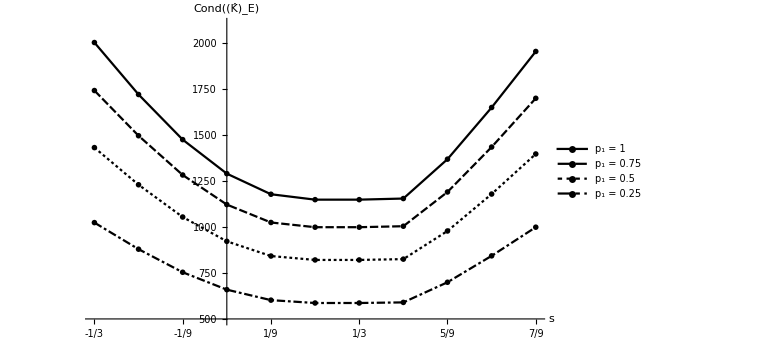

```mathematica
MechanicalLocalCond=Transpose[{s,√({13.061,9.6366,7.0840,5.4194,4.5195,4.2968,4.2970,4.3423,6.1015,8.8614,12.436}/(3.2614 10^-6))}];
Mechanicalr01p075Cond=Transpose[{s,√({9.7954,7.2272,5.3128,4.0643,3.3897,3.2222,3.2224,3.2566,4.5760,6.6458,9.3273}/(3.2337 10^-6))}];
Mechanicalr01p05Cond=Transpose[{s,√({6.5298,4.8178,3.5416,2.7094,2.2602,2.1476,2.1477,2.1709,3.0504,4.4302,6.2178}/(3.1910 10^-6))}];
Mechanicalr01p025Cond=Transpose[{s,√({3.2650,2.4090,1.7707,1.3545,1.1306,1.0730,1.0731,1.0852,1.5249,2.2147,3.1083}/(3.1191 10^-6))}];
(*Export["MechanicalCond.pdf",*)
ListLinePlot[{MechanicalLocalCond,Mechanicalr01p075Cond,Mechanicalr01p05Cond,Mechanicalr01p025Cond},ImageSize->Large,PlotTheme->"Monochrome",LabelStyle->Directive[{Black,FontSize->FS}],AxesLabel->{"s","Cond((K̂)_E)"},Ticks->{s,Automatic},PlotRange->{500,2100},
PlotLegends->Placed[{"p_1 = 1","p_1 = 0.75","p_1 = 0.5","p_1 = 0.25"},Scaled[{0.5,0.75}]]]
```